## Color Spaces and Information Storage for Computer Vision Processing

## Constructing a New Color Space

In order to construct a new color space, we need to consider the coordinate system of the new color space, the orientation of the new color space, and the fidelity of the discrete representation of the axes.

The first consideration is most easily decided; because there’s little obvious advantage otherwise, we choose a Cartesean coordinate system as this allows for a straightforward transformation involving only rotation, translation and scaling. Because we’re interested in the color information in the image, it’s useful to design the color space so there is a luminosity axis. This choice determines two of three rotational degrees of freedom, as will be discussed below.

As for the discrete representation of the axes, it’s desired that all the information captured pertaining to a hand should be preserved; all other information is irrelevant. However, here we’ll consider only the effect of a rotation and scaling on the discrete representation.

### Camera RGB and Normalization for Discrete Range

Due to the iPhone hardware being locked down at the application level, we do not have access to the raw camera feed. We do, however, have access to the post-processing (color-rebalanced and white-point-corrected) 8-bit RGB image data.

Because we’re searching for particular points in the real color space — which, being a continuous function, is infinite dimensional — there is a possibility in the future that larger multi-channel color spaces will be much more common, such as the 8-channel color spaces currently in development. Though most such cameras are primarily designed for post-production editing for still pictures and film (e.g. changing the lighting independent of the scene), as well as visual effects, the possibilities for computer vision are exciting. However, computer vision tasks are computationally intensive, and more often than not require operation in real time, so there is a natural inclination to shy away from large data sets in practical computer vision applications; many tasks are done in grayscale or single-channel processing to expedite the process.

As such, there is a need to develop techniques which keep the relevant information while quickly and efficiently discarding the irrelevant information. This is true for the RGB space at the moment, and the aim of this first part of the work.

### Rotation Matrix

Any rotation about an axis can be represented by a 3x3 square matrix in a 3D space. Since they are invertible, they’re guaranteed to be non-singular. However, as there are many ways in which to rotate an object from one position to another, or use a combination of different rotations to get to the same point, they aren’t necessarily unique. For this application, we require rotation about three different axes, which can be expressed thus:

```mathematica
ShowFun[RotationMatrixX[α]]
ShowFun[RotationMatrixY[β]]
ShowFun[RotationMatrixZ[γ]]
```

R_X(α) = (1 | 0 | 0
0 | cos(α) | sin(α)
0 | -sin(α) | cos(α))

R_Y(β) = (cos(β) | 0 | -sin(β)
0 | 1 | 0
sin(β) | 0 | cos(β))

R_Z(γ) = (cos(γ) | sin(γ) | 0
-sin(γ) | cos(γ) | 0
0 | 0 | 1)

```mathematica
Row[{MatrixForm[RotationMatrixX[α]],".",MatrixForm[RotationMatrixZ[γ]],".",MatrixForm[RotationMatrixY[β]]," =",MatrixForm[RotationMatrixXYZ[α,β, γ]]}]
```

(1 | 0 | 0
0 | Cos[α] | Sin[α]
0 | -Sin[α] | Cos[α]).(Cos[γ] | Sin[γ] | 0
-Sin[γ] | Cos[γ] | 0
0 | 0 | 1).(Cos[β] | 0 | -Sin[β]
0 | 1 | 0
Sin[β] | 0 | Cos[β]) =(1/2 (Cos[β-γ]+Cos[β+γ]) | Sin[γ] | 1/2 (-Sin[β-γ]-Sin[β+γ])
1/4 (2 Cos[α-β]-2 Cos[α+β]+Sin[α-β-γ]+Sin[α+β-γ]-Sin[α-β+γ]-Sin[α+β+γ]) | 1/2 (Cos[α-γ]+Cos[α+γ]) | 1/4 (-Cos[α-β-γ]+Cos[α+β-γ]+Cos[α-β+γ]-Cos[α+β+γ]+2 Sin[α-β]+2 Sin[α+β])
1/4 (Cos[α-β-γ]+Cos[α+β-γ]-Cos[α-β+γ]-Cos[α+β+γ]-2 Sin[α-β]+2 Sin[α+β]) | 1/2 (-Sin[α-γ]-Sin[α+γ]) | 1/4 (2 Cos[α-β]+2 Cos[α+β]+Sin[α-β-γ]-Sin[α+β-γ]-Sin[α-β+γ]+Sin[α+β+γ]))

Any rotation which orients the RGB color space such that one of the new axes lies along the luminosity direction is sufficient; a rotation which aligns the L axis along the luminosity direction is produced by a rotation of π/4 about the red (R) axis, followed by a rotation of arctan 1/(√2) about the green (G) axis.

```mathematica
Block[{n=10,θ=0,cube,m=24,steps,imgSize=500},
(* cube=RGBCubeFinite3D[n]; *)
cube=RGBCube3D[RGBCube["RGB"]];
steps=Flatten[{
Table[Graphics3D[Rotate[Rotate[Rotate[cube,g,{0,1,0}],0,{0,0,1}],0,{1,0,0}],Axes->True,PlotRange->{{0,Sqrt[3]},{-1,1},{-1,1}},ImageSize->imgSize,GraphicsCubeOpts],{g,0,Pi/4,Pi/(4m)}],
Table[Graphics3D[Rotate[Rotate[Rotate[cube,Pi/4,{0,1,0}],b,{0,0,1}],0,{1,0,0}],Axes->True,PlotRange->{{0,Sqrt[3]},{-1,1},{-1,1}},ImageSize->imgSize,GraphicsCubeOpts],{b,0,-ArcTan[1/Sqrt[2]],-ArcTan[1/Sqrt[2]]/m}],
Table[Graphics3D[Rotate[Rotate[Rotate[cube,Pi/4,{0,1,0}],-ArcTan[1/Sqrt[2]],{0,0,1}],r,{1,0,0}],Axes->True,PlotRange->{{0,Sqrt[3]},{-1,1},{-1,1}},ImageSize->imgSize,GraphicsCubeOpts],{r,0,Pi/4,Pi/(4m)}]
}];
ListAnimate[steps,AnimationRepetitions->1,AnimationRunning->False,AnimationRate->m,AnimationDirection->ForwardBackward]
]
```

This leaves one free rotational degree of freedom about the L axis. The resulting rotation matrix is given by:

```mathematica
ShowFun[RotationMatrixLCaCb[θ]]
```

R(θ) = (1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) sin(θ+π/6) | √(2/3) cos(θ) | -√(2/3) sin(π/6-θ)
-√(2/3) cos(θ+π/6) | -√(2/3) sin(θ) | √(2/3) cos(π/6-θ))

Where θ is the remaining rotational degree of freedom.

Using the standard rotation matrices, we get a luminosity axis which spans the range 0:√3. However, the length of the two remaining axes are dependent on the value of θ used. This is a problem because, ultimately, we want the axes to fit in a range of an appropriate data type. It would be more useful to have a matrix which provided the specified rotation and scaled the axis to known lengths. In the case of the luminosity, this is straightforward; simply divide by √3. In the case of the other two axes, we need an explicit form for the lengths of the axis resulting from the rotation.

Because the absolute values of the axes in the color space have no meaning, we’re only interested in the position along the axis relative to its start and end, equivalent to talking about the position in the axis relative to 0:1, compared to about 0:255 in unsigned, 8-bit integers. The upside is that if we’re rotating the cube about its corner, we’re interested in the minimum and maximum values possible along the new axis direction, which will correspond to a corner of the RGB cube. With the L axis aligned along the luminosity direction, the range of the L axis is 0 to √3. The x and y axes are symmetrical, spanning a range centered on 0. The range of their values is dependent upon the remaining degree of freedom.

We need to know, in each of the axes, how far out each point is. Because we’re effectively rotating a hexagon, whatever the answer is, we know the function is going to be periodic, repeating every π/3 radians, so we only have to solve it in the 0:π/3 region and then generalize. First we take the coordinates of the RGB cube and perform the rotation to find the values in the new color space.

```mathematica
Print[MatrixForm[LCaCb[θ]].MatrixForm[RGBCube],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[LCaCb[θ]. RGBCube]]],1]]
Print[MatrixForm[iLCaCb[θ]].MatrixForm[RGBCube["LCaCb"][θ]],"=",MatrixForm[Map[TrigFactor,FullSimplify[TrigFactor[iLCaCb[θ]. RGBCube["LCaCb"][θ]]]],1]]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]).(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)=(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

(1/(√3) | -√(2/3) Sin[π/6+θ] | -√(2/3) Cos[π/6+θ]
1/(√3) | √(2/3) Cos[θ] | -√(2/3) Sin[θ]
1/(√3) | -√(2/3) Sin[π/6-θ] | √(2/3) Cos[π/6-θ]).(0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)=(0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)

```mathematica
Row[{"RGBCube"["RGB"]," = ", MatrixForm[RGBCube["RGB"]],"    ","RGBCube"["LCaCb"][θ]," = ", MatrixForm[RGBCube["LCaCb"][θ]]}]
```

RGBCube[RGB] = (0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0 | 1 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1 | 1)    RGBCube[LCaCb][θ] = (0 | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | 1/(√3) | 2/(√3) | √3
0 | -√(2/3) Sin[π/6+θ] | √(2/3) Sin[π/6-θ] | √(2/3) Cos[θ] | √(2/3) Sin[π/6+θ] | -√(2/3) Sin[π/6-θ] | -√(2/3) Cos[θ] | 0
0 | -√(2/3) Cos[π/6+θ] | -√(2/3) Cos[π/6-θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6+θ] | √(2/3) Cos[π/6-θ] | √(2/3) Sin[θ] | 0)

The extent of the new axis is found by taking the maximum and minimum values of each row, i.e. the extreme corner positions relative to each new axis. An additional symmetry of the hexagonal projection of the RGB cube allows us to say that — whatever functional form is taken by one of the θ dependant ranges — the other can be found by a simple phase shift. So, recognizing that the minimum value is simply -1 times the maximum, we have simplified the problem to solving:

max(±(sin(θ))/(√6)±(cos(θ))/(√2),±√(2/3)sin(θ))  Where  0≤θ≤π/3

A graphical representation of the problem can be seen in Figure Section .

```mathematica
Manipulate[Block[{
maxRanges, ranges, cube, centersB, centersA, cols, imgScale, ticks,CbWidth, CbHeight,Cb,CaWidth,CaHeight,Ca,opt,cube3D}, 
   MaxTheta = Pi/2+0.2;
maxRanges = {{0, Sqrt[3]}, {-Sqrt[2/3], Sqrt[2/3]}, {-Sqrt[2/3], Sqrt[2/3]}};
imgScale = 200;
ranges = LCaCbAxisRanges[θ]; 
  cube = Cuboid[{{ranges[[1,1]], ranges[[2,1]], ranges[[3,1]]}, {ranges[[1,2]], ranges[[2,2]], ranges[[3,2]]}}]; 
  centersB = RGBCube["LCaCb"][θ][[3]];
centersA = RGBCube["LCaCb"][θ][[2]]; 
cols = MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]]; 
  ticks =Prepend[ Table[{N[i*(Pi/6)], i*(Pi/6)}, {i, 0, 6*(MaxTheta/Pi)}],{N[θ],"θ"}];
CbWidth  = maxRanges[[2,2]] - maxRanges[[2,1]] + MaxTheta; 
  CbHeight = maxRanges[[3,2]] - maxRanges[[3,1]];
Cb = Plot[Evaluate[RGBCube["LCaCb"][theta][[3]]], {theta, 0, MaxTheta}, 
         PlotStyle -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]], 
     FrameTicks -> {{All, None}, {None,ticks}}, 
         FrameLabel -> { {"RGB Cube corner position in Cb",None},{None,None}}, 
     PlotRange -> {{0, MaxTheta - maxRanges[[2,1]] + maxRanges[[2,2]]}, maxRanges[[3]]}, 
         Frame -> True, 
     Epilog -> Flatten[{Line[{{θ, -Sqrt[2/3]}, {θ, Sqrt[2/3]}}],
    {Opacity[0.8],  Table[{cols[[i]], Disk[{θ, centersB[[i]]}, 0.04]}, {i, 1, 8}]}, 
           {Black, Translate[Rectangle[Sequence @@ Transpose[{LCaCbAxisRanges[θ][[2]], LCaCbAxisRanges[θ][[3]]}]], {MaxTheta - maxRanges[[2,1]], 0}], 
            Blue, Translate[
          Polygon[LCaCbPolygon[θ], VertexColors -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]][[{2, 3, 4, 5, 6, 7}]]]]],
          {MaxTheta - maxRanges[[2,1]], 0}]
   }}], 
  AspectRatio -> CbHeight/CbWidth, 
      ImageSize -> Floor[imgScale*{CbWidth, CaHeight}]
]; 
CaWidth = maxRanges[[3,2]] - maxRanges[[3,1]] + MaxTheta; 
  CaHeight = maxRanges[[2,2]] - maxRanges[[2,1]];
Ca = Plot[Evaluate[RGBCube["LCaCb"][theta][[2]]], {theta, 0, MaxTheta}, 
         PlotStyle -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]]]], 
     FrameTicks -> {{All, None}, {ticks, None}}, 
         FrameLabel -> {None, "RGB Cube corner position in Ca"}, 
     PlotRange -> {{0, MaxTheta - maxRanges[[3,1]] + maxRanges[[3,2]]}, maxRanges[[2]]}, 
         Frame -> True, 
     Epilog -> Flatten[{Line[{{θ, -Sqrt[2/3]}, {θ, Sqrt[2/3]}}], 
    {Opacity[0.8], Table[{cols[[i]], Disk[{θ, centersA[[i]]}, 0.04]}, {i, 1, 8}]}, 
           {Black, Translate[Rectangle[Sequence @@ Transpose[{LCaCbAxisRanges[θ][[3]], LCaCbAxisRanges[θ][[2]]}]], {MaxTheta - maxRanges[[3,1]], 0}], 
            Blue, Translate[Polygon[LCaCbPolygon[θ - Pi/2], VertexColors -> MapThread[RGBColor, Transpose[Transpose[RGBCube["RGB"]][[
                {2, 3, 4, 5, 6, 7}]]]]], {MaxTheta - maxRanges[[3,1]], 0}]}}], 
     AspectRatio -> CaHeight/CaWidth, 
         ImageSize -> Floor[imgScale*{CaWidth, CaHeight}]
   ]; 

opt=GraphicsCubeOptions[ PlotRange->LCaCbAxisRanges[θ],ViewPoint->{8,5,-10},ImageSize->500];

cube3D=Flatten[{Opacity[1],RGBCubeInYabFinite[θ,cut],LCaCbAxisEnds3D[θ,brighten]}];

    Row[{Graphics3D[cube3D,opt],Show[Graphics[{
Inset[Cb, Floor[imgScale*{CbWidth, 0}], {CbWidth, maxRanges[[3,1]]}, Floor[imgScale*{CbWidth, CbHeight}]], 
       Inset[Ca, Floor[imgScale*{CaWidth, 0}], {CaWidth, maxRanges[[2,2]]}, Floor[imgScale*{CaWidth, CaHeight}], {0, -1}]}], 
     PlotRange -> Floor[imgScale*{{0, CbWidth}, {0, CaWidth}}],ImageSize->500]}]
]
, {θ, 0, MaxTheta},{brighten,1,2},{{cut,3},0,3}]
```

In the range 0:π/3, both sin and cos are positive, therefore the axis ranges are given by the following:

```mathematica
TableForm[LCaCbAxisRanges[θ],TableHeadings->{{"L","Ca","Cb"},{"Min","Max"}},TableAlignments->Center]
```

| Min | Max
L | 0 | √3
Ca | -√(2/3) Cos[π/6-Mod[-π/6+θ,π/3]] | √(2/3) Cos[π/6-Mod[-π/6+θ,π/3]]
Cb | -√(2/3) Cos[π/6-Mod[θ,π/3]] | √(2/3) Cos[π/6-Mod[θ,π/3]]

The lengths of the axis after rotation are given by:

```mathematica
Row[{"LCaCbAxisRanges"[θ]," = ",TraditionalForm[LCaCbAxisRanges[θ]/.{Mod[-π/6+θ,π/3]-> ϑ̃, Mod[θ,π/3]-> θ̃}],"  where  ", Column[{ϑ̃==Mod[-π/6+θ,π/3],θ̃ == Mod[θ,π/3]}]}]
```

LCaCbAxisRanges[θ] = (0 | √3
-√(2/3) cos(π/6-ϑ̃) | √(2/3) cos(π/6-ϑ̃)
-√(2/3) cos(π/6-θ̃) | √(2/3) cos(π/6-θ̃))  where  ϑ̃==Mod[-π/6+θ,π/3]
θ̃==Mod[θ,π/3]

```mathematica
Manipulate[Block[{maxRanges,ranges, cube},
maxRanges = {{0,√3},{-√(2/3),√(2/3)},{-√(2/3),√(2/3)}};
ranges = LCaCbAxisRanges[θ];
cube = Cuboid[{{ranges[[1,1]],ranges[[2,1]],ranges[[3,1]]},{ranges[[1,2]],ranges[[2,2]],ranges[[3,2]]}}];
Grid[{{Show[
Graphics[Raster[Table[Table[inLCaCb[θ].{Y,a,b},{a,-0.5,0.5,0.02}],{b,-0.5,0.5,0.02}]]]
,ImageSize->400],Graphics[{Black,Rectangle[Sequence@@Transpose[{LCaCbAxisRanges[θ ][[2]],LCaCbAxisRanges[θ ][[3]]}]],Blue,Polygon[LCaCbPolygon[θ],VertexColors->MapThread[RGBColor,Transpose[Transpose[RGBCube["RGB"]][[{2,3,4,5,6,7}]]]]]},PlotRange->{maxRanges[[2]],maxRanges[[3]]},ImageSize->400]}}]
],{θ,0,Pi},{{Y,0.5},0,1}]
```

It is convenient to produce a transformation which will result in axes of known length. Because the rotation cannot include a translation, we desire a transformation matrix which will result in the ranges 0:1, -1/2:1/2, and -1/2:1/2. Such a transformation is easily obtained by multiplying the rotation matrix by a diagonal matrix with the reciprocal of the maximums found above placed along the diagonal. This will scale each axis to a unit length.

```mathematica
Replace[ShowFun[scale["LCaCb","nLCaCb"][θ]],{List->mForm },{4},Heads->True]
Replace[ShowFun[scale["nLCaCb","LCaCb"][θ]],{List->mForm },{4},Heads->True]
```

L(θ) = ( TagBox[GridBox[{{√3}, {2 √2/3 cos(π/6 - TemplateBox[List[RowBox[List[

L^-1(θ) = ( TagBox[GridBox[{{1/√3}, {1/2 √3/2 sec(π/6 - TemplateBox[List[RowBox[List[

The normalized ’rotation’ matrix is given by:

```mathematica
Print["nLCaCb[θ] = ",MatrixForm[nLCaCb[θ]]]
```

nLCaCb[θ] = (1/3 | 1/3 | 1/3
-1/2 Sec[π/6-Mod[-π/6+θ,π/3]] Sin[π/6+θ] | 1/2 Cos[θ] Sec[π/6-Mod[-π/6+θ,π/3]] | -1/2 Sec[π/6-Mod[-π/6+θ,π/3]] Sin[π/6-θ]
-1/2 Cos[π/6+θ] Sec[π/6-Mod[θ,π/3]] | -1/2 Sec[π/6-Mod[θ,π/3]] Sin[θ] | 1/2 Cos[π/6-θ] Sec[π/6-Mod[θ,π/3]])

This matrix is no longer technically a rotation matrix as its inverse is no longer equal to its transpose. It now equal to:

nLCaCb( θ ) = L^-1( θ ) ⊗ LCaCb( θ ) 
  
  nLCaCb^-1 = ( (L( θ ) ⊗ LCaCb( θ )   ))^T

```mathematica
Print["inLCaCb[θ] =",MatrixForm[inLCaCb[θ]]]
```

inLCaCb[θ] =(1 | 1/3 (-2 Cos[π/6-θ+Mod[π/6+θ,π/3]]-2 Sin[θ+Mod[π/6+θ,π/3]]) | 1/3 (-2 Cos[θ+Mod[θ,π/3]]-2 Sin[π/6-θ+Mod[θ,π/3]])
1 | 4/3 Cos[θ] Cos[π/6-Mod[π/6+θ,π/3]] | -4/3 Cos[π/6-Mod[θ,π/3]] Sin[θ]
1 | 1/3 (-2 Cos[π/6+θ+Mod[π/6+θ,π/3]]+2 Sin[θ-Mod[π/6+θ,π/3]]) | 1/3 (2 Cos[θ-Mod[θ,π/3]]+2 Sin[π/6+θ+Mod[θ,π/3]]))

```mathematica
Clear[inLCaCbFun,inLCaCb];
inLCaCbFun=Function[{θ},Evaluate[Transpose[scale["LCaCb","nLCaCb"][θ] LCaCb[θ]]]];
inLCaCb[θ:Except[_String]]:=inLCaCbFun[θ]
Format[inLCaCb, TraditionalForm]=Superscript[Style["nLCaCb",Bold],"-1"];
ShowFun[inLCaCb[θ]]
```

nLCaCb^-1(θ) = (1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(θ+π/6) | -4/3 cos(θ+π/6) cos(π/6-θπ/3)
1 | 4/3 cos(θ) cos(π/6-(θ-π/6)π/3) | -4/3 cos(π/6-θπ/3) sin(θ)
1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(π/6-θ) | 4/3 cos(π/6-θ) cos(π/6-θπ/3))

```mathematica
Row[{inLCaCb["θ"],".",nLCaCb["θ"]," = ",MatrixForm[FullSimplify[inLCaCb[θ] . nLCaCb[θ]]]}]
```

inLCaCb[θ].nLCaCb[θ] = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Style[TraditionalForm[Row[{nLCaCb["θ"]," = ",scale["nLCaCb","LCaCb"]["θ"]," ⊗ ",LCaCb["θ"]}]],Larger]
Style[TraditionalForm[Row[{nLCaCb["θ"]," = ",MatrixForm[scale["nLCaCb","LCaCb"][θ]]," ⊗ ",MatrixForm[LCaCb[θ]]}]],Larger]
```

nR(θ) = L^-1(θ) ⊗ R(θ)

nR(θ) = (1/(√3)
1/2 √(3/2) sec(π/6-(θ-π/6)π/3)
1/2 √(3/2) sec(π/6-θπ/3)) ⊗ (1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) sin(θ+π/6) | √(2/3) cos(θ) | -√(2/3) sin(π/6-θ)
-√(2/3) cos(θ+π/6) | -√(2/3) sin(θ) | √(2/3) cos(π/6-θ))

```mathematica
ShowFun[nLCaCb[θ]]
ShowFun[inLCaCb[θ]]
```

nR(θ) = (1/3 | 1/3 | 1/3
-1/2 sec(π/6-(θ-π/6)π/3) sin(θ+π/6) | 1/2 cos(θ) sec(π/6-(θ-π/6)π/3) | -1/2 sec(π/6-(θ-π/6)π/3) sin(π/6-θ)
-1/2 cos(θ+π/6) sec(π/6-θπ/3) | -1/2 sec(π/6-θπ/3) sin(θ) | 1/2 cos(π/6-θ) sec(π/6-θπ/3))

nLCaCb^-1(θ) = (1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(θ+π/6) | -4/3 cos(θ+π/6) cos(π/6-θπ/3)
1 | 4/3 cos(θ) cos(π/6-(θ-π/6)π/3) | -4/3 cos(π/6-θπ/3) sin(θ)
1 | -4/3 cos(π/6-(θ-π/6)π/3) sin(π/6-θ) | 4/3 cos(π/6-θ) cos(π/6-θπ/3))

### Representing the Rotation

The final piece of the metaphorical jigsaw is to add the capability to deal with the machine handling of the numerics. The transforms as defined above assume the capacity to represent the resulting numbers. Unfortunately, on a device, the numerics are not handled in such a pure way and — whilst we are uninterested in the information overflow outside the destination representation — this can cause instabilities in a practical implementation. In the development of the algorithm, it is therefore necessary to define these bounds. In the unit space, these bounds have already been defined by Equation Section ; so long as the axis length can be represented on the device between these bounds, then overflow and underflow can be dealt with using a simple conditional statement.

It is significantly advantageous to perform calculations using integer types, particularly given that the input and output types are integers with small ranges, meaning it’s possible to construct algorithms which avoid conversion to floating point operations. To this end, we wish to determine the most efficient internal representation for the transformation.

#### Principles of Optimization

During the color space conversion, the pixel values are represented in three different ways: input, working and output representations. At each stage, we are concerned with preserving the information from the previous stage required by the next. For this reason, we have defined terms for the mathematical analysis of the problem, as well as terms for the algorithm development. The terms associated with each stage are as follows:

Data Types   |  Src Pixel Values   |  Trans Pixel Values   |  Dst Pixel Values  
 What?   |  Input   |  Working   |  Output  
 Where?   |  Initial   |  After Rotation   |  After Re-Distribution  
 Unit Range Value   |     |     |    
 1-1 Int Range Value   |     |     |    
 1-1 Max   |     |     |    
 1-1 Min   |     |     |    
 1-1 Range   |     |     |

The rotation operation consists of 9 multiplications and 6 additions and constitutes the majority of the computational cost. It is this operation which we will focus our optimization efforts upon. The redistribution transformation, which comes after the rotation, processes each pixel channel value separately. This allows us to pull apart the rotation matrix by scaling each row arbitrarily, handing the knowledge of the scaling to the distribution. The goal of this section is to represent the matrix multiplication in such a way that we avoid floating-point operations.

R[θ]==(-
Scale
-)⊗qR[θ]          where      qR[θ]∈Z

Given an infinite set of integers, this is not a problem. However, we wish to choose  to lie in a finite range, which depends on the color depth of the source. Ideally, we’d like the result of the rotation to have a bit depth not greater than twice the bit depth of the source, i.e. for 8-bit pixel values, we would like the rotated LCaCb values to be expressible as 16-bit integers. To accommodate 3 multiplications and 2 additions, the matrix  needs to be represented in two fewer bits than the source.

This unit range is discretized into steps of 1/srcRangeand 1/tRange. The question then is to what degree of accuracy do we need to represent the internal numerics? If we represent the transformation in a discrete type , we can express the problem in terms of the largest perturbation which can be made to the transformation without affecting the result.

·  |  ==  |  let    |  ==+ 
 (+)·  |  ==+  |  | 
 therefore if ·  |  ==  |  then  ·==  |

The continuous rotation  can be expressed as the sum of its discrete representation  with a discretization factor  and the correction . The elements of the discrete rotation can be expressed as rational fractions.

(==int(·))/(where  int(1.5)==1,int(-1.5)==-1)
((therefore  -1)/(<<1))/

It should be noted that — unlike the source type — the perturbation can be negative. The definition of the function int results in the sign of the perturbation matching the sign of the discretized transformation matrix. We must therefore consider both the maximum and minimum of . As 0≤≤1 the extrema of  are found where  is a vector with elements of 0 and 1. If the matrix is decomposed into a sum of positive and negative elements (==)_++_- then the extrema are given by max(_+·1) and min(_-·1). Where the elements are positive or negative is determined by the sign of the elements in the rotation matrix .

#### Factoring the Rotation

If we were to scale the entire matrix evenly, the top row would dominate as it is always positive, and the necessary discrete representation would be characterised by ==3 . This would, however, necessitate the matrix being stored in a data type with at least 2 more bits than the source type.

The second and third rows each sum to zero (·1==[√3,0,0], where 1 is a vector of ones), allowing us to state that each of the rows has one element of the opposite sign to the other two elements. The discretization for the second and third rows then only requires ==2 . It is also possible to pull out common factors from the rows, resulting in all elements taking values between -1 and 1.

A reduced form for the matrix part of the rotation is
LCaCb( θ ) = (1/(√3)
√(2/3)
√(2/3)) ⊗ rR( θ )

```mathematica
Row[{MatrixForm[RotationMatrixLCaCb[θ]]," = ",MatrixForm[scale["LCaCb","rR"][θ]],"⊗",MatrixForm[rR[θ]]}]
```

(1/(√3) | 1/(√3) | 1/(√3)
-√(2/3) Sin[π/6+θ] | √(2/3) Cos[θ] | -√(2/3) Sin[π/6-θ]
-√(2/3) Cos[π/6+θ] | -√(2/3) Sin[θ] | √(2/3) Cos[π/6-θ]) = (1/(√3)
√(2/3)
√(2/3))⊗(1 | 1 | 1
-Sin[π/6+θ] | Cos[θ] | -Sin[π/6-θ]
-Cos[π/6+θ] | -Sin[θ] | Cos[π/6-θ])

```mathematica
StringJoin[mForm[scale["LCaCb","rR"]] ,"⊗", mForm[ rR[θ]],mForm[{r,g,b}]," = ",mForm[{x,y,z}]]
StringJoin[ mForm[ irR[θ]],mForm[{{mForm[scale["LCaCb","rR"]] ,"⊗",mForm[{x,y,z}]}}]," = ",mForm[{r,g,b}]]
```

( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] )⊗1 | 1 | 1
-sin(θ + π/6) | cos(θ) | -sin(π/6 - θ)
-cos(θ + π/6) | -sin(θ) | cos(π/6 - θ)r
g
b = x
y
z

1 | -sin(θ + π/6) | -cos(θ + π/6)
1 | cos(θ) | -sin(θ)
1 | -sin(π/6 - θ) | cos(π/6 - θ)( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] ) | ⊗ | x
y
z = r
g
b

Because rR is factored from a rotation matrix the inverse is

```mathematica
LCaCb^(-1 =)(({{1/(√3)}, {√(2/3)}, {√(2/3)}}) ⊗ ({{1, 1, 1}, {-Sin[π/6+θ], Cos[θ], -Sin[π/6-θ]}, {-Cos[π/6+θ], -Sin[θ], Cos[π/6-θ]}}))^T
rR =({{√3}, {√(3/2)}, {√(3/2)}}) ⊗({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}})
```

using
A = s ⊗ B    where B^-1= B^T
A^-1=  (s^-1 ⊗ B)^T

```mathematica
rR^-1 =(({{1/(√3)}, {√(2/3)}, {√(2/3)}}) ⊗({{1/(√3), 1/(√3), 1/(√3)}, {-√(2/3) Sin[π/6+θ], √(2/3) Cos[θ], -√(2/3) Sin[π/6-θ]}, {-√(2/3) Cos[π/6+θ], -√(2/3) Sin[θ], √(2/3) Cos[π/6-θ]}}))^T = ({{1/3, -2/3 Sin[π/6+θ], -2/3 Cos[π/6+θ]}, {1/3, (2 Cos[θ])/3, -(2 Sin[θ])/3}, {1/3, -2/3 Sin[π/6-θ], 2/3 Cos[π/6-θ]}})
```

Proof of inverse

```mathematica
MatrixForm[Simplify[irR[θ].rR[θ]]]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

To facilitate the quantization, we next factor the second and third rows such that the largest element of each row equals exactly 1. As previously mentioned, the largest element has the opposite sign to the other two elements in a given row. So, the steps required to perform the factorization are as follows:

Find the sign of each of the elements.

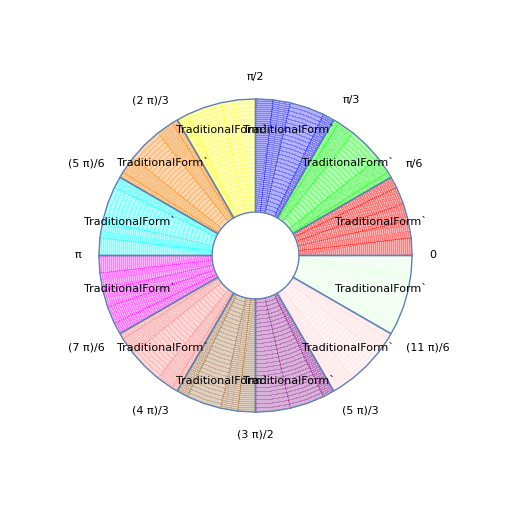

```mathematica
partShow[Piecewise[{
 {mForm[Sign[nonNegativeSign[rR[    Pi /12]]]], Inequality[0,         LessEqual, θ, Less,    Pi/6]}, 
    {mForm[Sign[nonNegativeSign[rR[    Pi /4 ]]]], Inequality[Pi/6,      LessEqual, θ, Less,    Pi/3]}, 
    {mForm[Sign[nonNegativeSign[rR[(5 *Pi)/12]]]], Inequality[Pi/3,      LessEqual, θ, Less,    Pi/2]}, 
    {mForm[Sign[nonNegativeSign[rR[(7 *Pi)/12]]]], Inequality[Pi/2,      LessEqual, θ, Less, (2*Pi)/3]}, 
    {mForm[Sign[nonNegativeSign[rR[(3 *Pi)/4 ]]]], Inequality[(2*Pi)/3,  LessEqual, θ, Less, (5*Pi)/6]}, 
    {mForm[Sign[nonNegativeSign[rR[(11*Pi)/12]]]], Inequality[(5*Pi)/6,  LessEqual, θ, Less,    Pi]}, 
    {mForm[Sign[nonNegativeSign[rR[(13*Pi)/12]]]], Inequality[   Pi,     LessEqual, θ, Less, (7*Pi)/6]}, 
    {mForm[Sign[nonNegativeSign[rR[(5 *Pi)/4 ]]]], Inequality[(7*Pi)/6,  LessEqual, θ, Less, (4*Pi)/3]}, 
    {mForm[Sign[nonNegativeSign[rR[(17*Pi)/12]]]], Inequality[(4*Pi)/3,  LessEqual, θ, Less, (3*Pi)/2]}, 
    {mForm[Sign[nonNegativeSign[rR[(19*Pi)/12]]]], Inequality[(3*Pi)/2,  LessEqual, θ, Less, (5*Pi)/3]}, 
    {mForm[Sign[nonNegativeSign[rR[(7 *Pi)/4 ]]]], Inequality[(5*Pi)/3,  LessEqual, θ, Less, (11*Pi)/6]}, 
    {mForm[Sign[nonNegativeSign[rR[(23*Pi)/12]]]], Inequality[(11*Pi)/6, LessEqual, θ, Less,  2*Pi]}}, Null]]
```

Determine which of those elements is of the opposite sign.

```mathematica
partShow[Piecewise[{
{mForm[matSameSign[rR[Pi/12]]], Inequality[0, LessEqual, θ, Less, Pi/6]||Inequality[         Pi       , LessEqual, θ, Less, (7*Pi)/6]}, 
   {mForm[matSameSign[rR[        Pi   /  4  ]]], Inequality[        Pi/  6, LessEqual, θ, Less, Pi/3]||Inequality[(7*Pi)/6, LessEqual, θ, Less, (4*Pi)/3]}, 
   {mForm[matSameSign[rR[(  5*Pi)/12]]], Inequality[        Pi/  3, LessEqual, θ, Less, Pi/2]||Inequality[(4*Pi)/3, LessEqual, θ, Less, (3*Pi)/2]}, 
   {mForm[matSameSign[rR[(  7*Pi)/12]]], Inequality[        Pi/  2, LessEqual, θ, Less, (2*Pi)/3]||Inequality[(3*Pi)/2, LessEqual, θ, Less, (5*Pi)/3]}, 
   {mForm[matSameSign[rR[(  3*Pi)/  4]]], Inequality[(2*Pi)/3, LessEqual, θ, Less, (5*Pi)/6]||Inequality[(5*Pi)/3, LessEqual, θ, Less, (11*Pi)/6]}, 
   {mForm[matSameSign[rR[(11*Pi)/12]]], Inequality[(5*Pi)/6, LessEqual, θ, Less, Pi]||Inequality[(11*Pi)/6, LessEqual, θ, Less, 2*Pi]}}, Null]]
```

-Graphics-

Factor each row by that largest element.

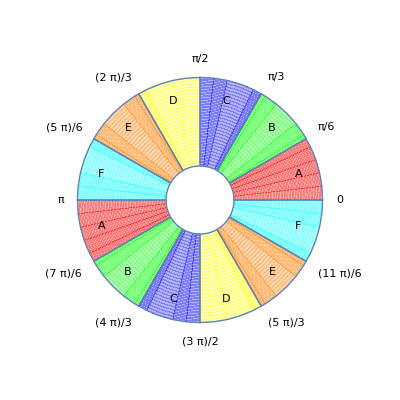
The Factored Rotation in each π/6 Region
-Graphics- | Scale : fS[θ] | Factored Rotation : fR[θ]
A | 1
cos(θ)
cos(π/6 - θ) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
B | 1
-sin(θ + π/6)
cos(π/6 - θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
C | 1
-sin(θ + π/6)
-sin(θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
D | 1
-sin(π/6 - θ)
-sin(θ) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
E | 1
-sin(π/6 - θ)
-cos(θ + π/6) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))
F | 1
cos(θ)
-cos(θ + π/6) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[scale["rR","fR"][θ][[1,1,1]]],TraditionalForm[fR[θ][[1,1,1]]]},
{mForm[scale["rR","fR"][θ][[1,2,1]]],TraditionalForm[fR[θ][[1,2,1]]]},
{mForm[scale["rR","fR"][θ][[1,3,1]]],TraditionalForm[fR[θ][[1,3,1]]]},
{mForm[scale["rR","fR"][θ][[1,4,1]]],TraditionalForm[fR[θ][[1,4,1]]]},
{mForm[scale["rR","fR"][θ][[1,5,1]]],TraditionalForm[fR[θ][[1,5,1]]]},
{mForm[scale["rR","fR"][θ][[1,6,1]]],TraditionalForm[fR[θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fS[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The sign of the elements is most easily seen by looking at the rotation as phase shifted sine functions.

```mathematica
Clear[splitCircle]
splitCircle[i_, θ_, val_:1] := Module[{showA, evalA, showB, evalB}, 
   Piecewise[{{val, CircularInequality[i*(Pi/6), LessEqual, θ, Less, (i + 6)*(Pi/6)]}, 
     {-val, CircularInequality[(i - 6)*(Pi/6), LessEqual, θ, Less, i*(Pi/6)]}}, Null]]
```

```mathematica
posNegCond=Function[{θ},Evaluate[{{1,1,1},{splitCircle[5,θ],splitCircle[9,θ],splitCircle[1,θ]},
{splitCircle[2,θ],splitCircle[6,θ,1],splitCircle[10,θ,1]}}]];
TraditionalForm[MatrixForm[posNegCond[θ]]]
```

(1 | 1 | 1
Piecewise[{{1, (5 π)/6≤θ<(11 π)/6}, {-1, -π/6≤θ<(5 π)/6}, {Null, True}}] | Piecewise[{{1, -π/2≤θ<π/2}, {-1, π/2≤θ<(3 π)/2}, {Null, True}}] | Piecewise[{{1, π/6≤θ<(7 π)/6}, {-1, -(5 π)/6≤θ<π/6}, {Null, True}}]
Piecewise[{{1, π/3≤θ<(4 π)/3}, {-1, -(2 π)/3≤θ<π/3}, {Null, True}}] | Piecewise[{{1, -π≤θ<0}, {-1, 0≤θ<π}, {Null, True}}] | Piecewise[{{1, -π/3≤θ<(2 π)/3}, {-1, (2 π)/3≤θ<(5 π)/3}, {Null, True}}])

So the signs look like

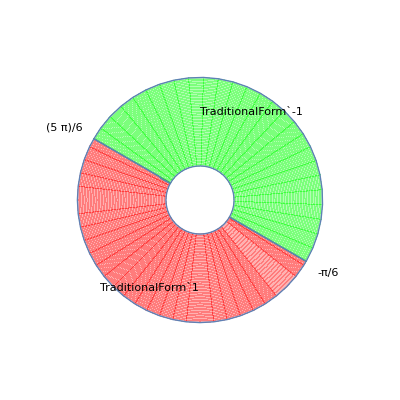
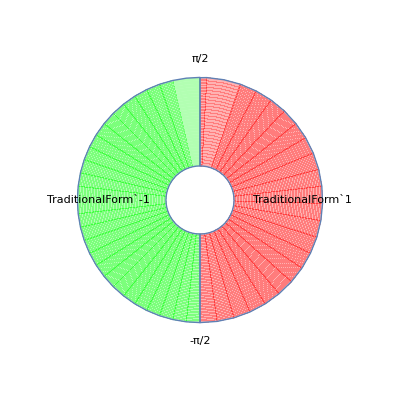
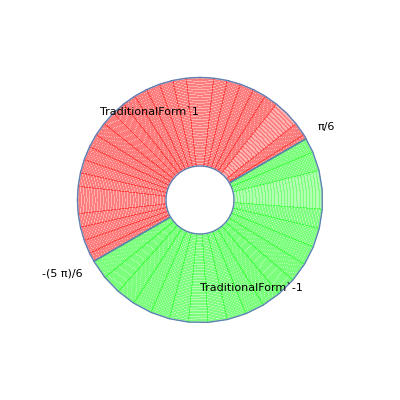
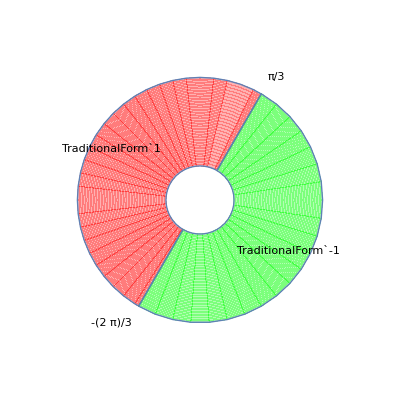
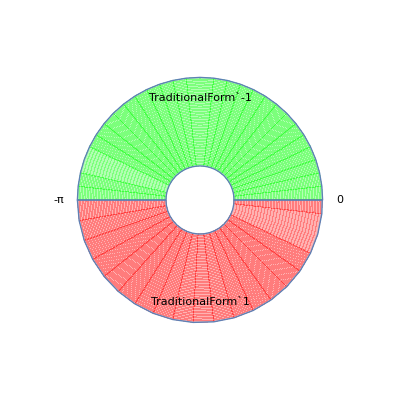
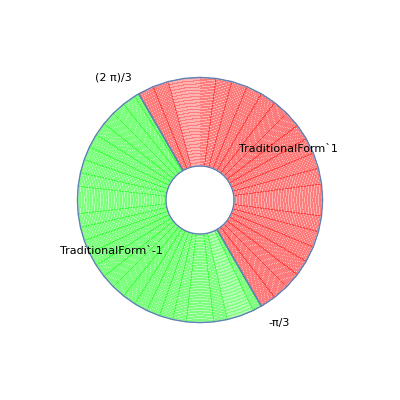
(1 | 1 | 1
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-)

```mathematica
MatrixForm[{{1,1,1},{partShow[splitCircle[5,θ]],partShow[splitCircle[9,θ]],partShow[splitCircle[1,θ]]},
{partShow[splitCircle[2,θ]],partShow[splitCircle[6,θ,1]],partShow[splitCircle[10,θ,1]]}}]
```

Each row is a series of three sin waves each (2π)/3 out of phase with each other. The rows areπ/2 out of phase with each other. The largest element changes every π/6 radians repeating every π radians.

rR[θ]=(1 | 1 | 1
sin(θ-(5π)/6) | sin(θ+(3π)/6) | sin(θ-π/6)
sin(θ-(2 π)/6) | sin(θ-(6 π)/6) | sin(θ+(2π)/6))

By defining θ as θ==Θ+ — where ==θ      mod6, and Θ is the starting value for the region in which θ lies — and substituting in the function [ϕ]:

[ϕ]  |  ==1/2(1+√3 tan(ϕ))

we can now rewrite the factored rotation as shown in

```mathematica
fR=Function[{θ},Evaluate[ApplyToPiecewise[(rR[θ]/#)&,scale["rR","fR"][θ]]]];
```

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[scale["rR","fR"][θ][[1,1,1]]],TraditionalForm[fR[θ][[1,1,1]]]},
{mForm[scale["rR","fR"][θ][[1,2,1]]],TraditionalForm[fR[θ][[1,2,1]]]},
{mForm[scale["rR","fR"][θ][[1,3,1]]],TraditionalForm[fR[θ][[1,3,1]]]},
{mForm[scale["rR","fR"][θ][[1,4,1]]],TraditionalForm[fR[θ][[1,4,1]]]},
{mForm[scale["rR","fR"][θ][[1,5,1]]],TraditionalForm[fR[θ][[1,5,1]]]},
{mForm[scale["rR","fR"][θ][[1,6,1]]],TraditionalForm[fR[θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fS[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The Factored Rotation in each π/6 Region
-Graphics- | Scale : fS[θ] | Factored Rotation : fR[θ]
A | 1
cos(θ)
cos(π/6 - θ) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
B | 1
-sin(θ + π/6)
cos(π/6 - θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
-cos(θ+π/6) sec(π/6-θ) | -sec(π/6-θ) sin(θ) | 1)
C | 1
-sin(θ + π/6)
-sin(θ) | (1 | 1 | 1
1 | -cos(θ) csc(θ+π/6) | csc(θ+π/6) sin(π/6-θ)
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
D | 1
-sin(π/6 - θ)
-sin(θ) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
cos(θ+π/6) csc(θ) | 1 | -cos(π/6-θ) csc(θ))
E | 1
-sin(π/6 - θ)
-cos(θ + π/6) | (1 | 1 | 1
csc(π/6-θ) sin(θ+π/6) | -cos(θ) csc(π/6-θ) | 1
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))
F | 1
cos(θ)
-cos(θ + π/6) | (1 | 1 | 1
-sec(θ) sin(θ+π/6) | 1 | -sec(θ) sin(π/6-θ)
1 | sec(θ+π/6) sin(θ) | -cos(π/6-θ) sec(θ+π/6))

Let θ1 = Mod[θ,Pi/6]
Let Θ = θ-θ1
then
θ = Θ+θ1
also the regions can be simplified by noticing that they are in modulo π arithmatic so θ→Mod[θ,π]

```mathematica
ffR=Function[{θ},Evaluate[
Piecewise@Table[{Assuming[Element[θ1,Reals]&& θ1≥ 0 && θ1< Pi/6,FullSimplify[fR[θ][[1,i+1,1]]/.{θ->i Pi/6 +θ1}]],FullSimplify[fR[θ][[1,i+1,2,1]]/.{Mod[θ,2 π]-> Mod[θ,π]} ]},{i,0,5}]]];
```

```mathematica
Definition[ffR]
```

```mathematica
ApplyToPiecewise[mForm,ffR[θ]]
```

Piecewise[{{1 | 1 | 1
sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1)
-cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1))
1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1))
sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
-cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1
sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1), π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)) | 1
1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1) | sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
sin(TraditionalForm`θ_1) (-sec(π/6 - TraditionalForm`θ_1)) | 1 | -cos(TraditionalForm`θ_1 + π/6) sec(π/6 - TraditionalForm`θ_1)
1 | 1/2 (√3 tan(TraditionalForm`θ_1) - 1) | sin(TraditionalForm`θ_1 + π/6) (-sec(TraditionalForm`θ_1)), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

There are only 4 functions

```mathematica
Clear[ffRList,fReq,fRe,ffRe]
```

```mathematica
ffRList=Function[{δθ},Evaluate@ApplyToPiecewise[Union[Flatten[#]]&,ffR[θ]][[1,1,1]]]
```

Function[{δθ},{1,-Cos[π/6+δθ] Sec[π/6-δθ],-Sec[π/6-δθ] Sin[δθ],-Sec[δθ] Sin[π/6+δθ],1/2 (-1+√3 Tan[δθ])}]

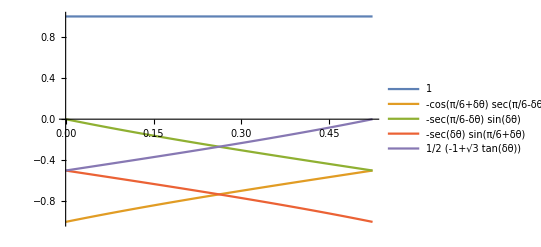

```mathematica
Plot[Evaluate[ffRList[δθ]],{δθ,0,Pi/6},PlotLegends->"Expressions"]
```

using

```mathematica
If[FullSimplify[#],TraditionalForm[#]]&[-Cos[π/6+θ1] Sec[π/6-θ1]==-1/2 (1+√3 Tan[π/6-θ1])]
If[FullSimplify[#],TraditionalForm[#]]&[-Sec[π/6-θ1] Sin[θ1] ==-1/2 (1+√3 Tan[θ1-π/6])]
If[FullSimplify[#],TraditionalForm[#]]&[-Sec[θ1] Sin[π/6+θ1]==-1/2 (1+√3 Tan[θ1])]
```

-cos(θ_1+π/6) sec(π/6-θ_1)==1/2 (-√3 tan(π/6-θ_1)-1)

sin(θ_1) (-sec(π/6-θ_1))==1/2 (√3 tan(π/6-θ_1)-1)

sin(θ_1+π/6) (-sec(θ_1))==1/2 (-√3 tan(θ_1)-1)

Defining a common function for the elements

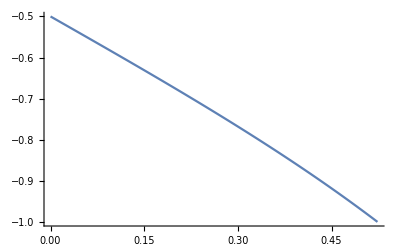

```mathematica
fRe=Function[{θ},-1/2 (1+√3 Tan[θ])];
Plot[Evaluate[fRe[θ]],{θ,0,Pi/6},PlotLegends->"Expressions"]
```

```mathematica
fReList=Function[{θ1},{fRe[π/6-θ1],fRe[θ1-π/6],fRe[θ1],fRe[-θ1]}];
Plot[Evaluate[fReList[θ1]],{θ1,0,Pi/6},PlotLegends->"Expressions"]
```

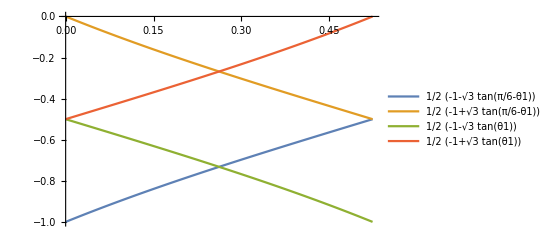

we can write fR as

```mathematica
ffRe=Function[{θ,θ1,fReqq},Evaluate[ApplyToPiecewise[
(#/.{-Cos[π/6+θ1] Sec[π/6-θ1]-> fReqq[π/6-θ1],-Sec[π/6-θ1] Sin[θ1]-> fReqq[θ1-π/6],-Sec[θ1] Sin[π/6+θ1]-> fReqq[θ1],1/2 (-1+√3 Tan[θ1])-> fReqq[-θ1]})&,ffR[θ]]]];
```

```mathematica
Row[{"fR(θ) = ",ApplyToPiecewise[mForm,ffRe[θ,θ1,"fRe"]]," = ",ApplyToPiecewise[mForm,ffRe[θ,θ1,fRe]]}]
```

fR(θ) = Piecewise[{{1 | 1 | 1
fRe | 1 | -
fRe | - | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | fRe | -
- | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
- | fRe | 1
1 | fRe | -, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
- | 1 | fRe
1 | - | fRe, (5 π)/6≤Mod[θ,π]<π}, {0, True}}] = Piecewise[{{1 | 1 | 1
1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) + 1) - 1
1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) + 1) - 1 | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) + 1) - 1
1/2 (√3 tan(TraditionalForm`θ_1) + 1) - 1 | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | 1/2 (√3 tan(TraditionalForm`θ_1) + 1) - 1 | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1)
1/2 (√3 tan(π/6 - TraditionalForm`θ_1) + 1) - 1 | 1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1), π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) + 1) - 1 | 1
1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1 | 1/2 (√3 tan(TraditionalForm`θ_1) + 1) - 1, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
1/2 (√3 tan(TraditionalForm`θ_1) + 1) - 1 | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1) | 1
1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1) | 1/2 (√3 tan(π/6 - TraditionalForm`θ_1) + 1) - 1, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
1/2 (√3 tan(π/6 - TraditionalForm`θ_1) + 1) - 1 | 1 | 1/2 (-√3 tan(π/6 - TraditionalForm`θ_1) - 1)
1 | 1/2 (√3 tan(TraditionalForm`θ_1) + 1) - 1 | 1/2 (-√3 tan(TraditionalForm`θ_1) - 1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[scale["rR","fR"][θ][[1,1,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,1,1]]]},
{mForm[scale["rR","fR"][θ][[1,2,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,2,1]]]},
{mForm[scale["rR","fR"][θ][[1,3,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,3,1]]]},
{mForm[scale["rR","fR"][θ][[1,4,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,4,1]]]},
{mForm[scale["rR","fR"][θ][[1,5,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,5,1]]]},
{mForm[scale["rR","fR"][θ][[1,6,1]]],TraditionalForm[ffRe[θ,θ1,"fRe"][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fS[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The Factored Rotation in each π/6 Region
-Graphics- | Scale : fS[θ] | Factored Rotation : fR[θ]
A | 1
cos(θ)
cos(π/6 - θ) | (1 | 1 | 1
fRe(θ_1) | 1 | fRe(-θ_1)
fRe(π/6-θ_1) | fRe(θ_1-π/6) | 1)
B | 1
-sin(θ + π/6)
cos(π/6 - θ) | (1 | 1 | 1
1 | fRe(π/6-θ_1) | fRe(θ_1-π/6)
fRe(-θ_1) | fRe(θ_1) | 1)
C | 1
-sin(θ + π/6)
-sin(θ) | (1 | 1 | 1
1 | fRe(-θ_1) | fRe(θ_1)
fRe(θ_1-π/6) | 1 | fRe(π/6-θ_1))
D | 1
-sin(π/6 - θ)
-sin(θ) | (1 | 1 | 1
fRe(π/6-θ_1) | fRe(θ_1-π/6) | 1
fRe(θ_1) | 1 | fRe(-θ_1))
E | 1
-sin(π/6 - θ)
-cos(θ + π/6) | (1 | 1 | 1
fRe(-θ_1) | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | fRe(θ_1-π/6))
F | 1
cos(θ)
-cos(θ + π/6) | (1 | 1 | 1
fRe(θ_1-π/6) | 1 | fRe(π/6-θ_1)
1 | fRe(-θ_1) | fRe(θ_1))

The Relationship

```mathematica
Reduce[-1-fRe[θ]==fRe[-θ]]
```

True

alows us to write another interesting form

```mathematica
ffRe=Function[{θ,θ1,fReqq},Evaluate[ApplyToPiecewise[
(#/.{ fReqq[θ1-π/6]-> -1-fReqq[π/6-θ1], fReqq[-θ1]-> -1-fReqq[θ1]})&,ffRe[θ,θ1,fReqq]]]];
```

```mathematica
Row[{"fR(θ) = ",ApplyToPiecewise[mForm,ffRe[θ,θ1,"fRe"]]}]
```

fR(θ) = Piecewise[{{1 | 1 | 1
fRe | 1 | -
fRe | - | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | fRe | -
- | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
- | fRe | 1
1 | fRe | -, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
- | 1 | fRe
1 | - | fRe, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

```mathematica
Row[{ShowFun[fR[θ6,θ1,"fRe"]],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]
```

fR(θ6,θ1,fRe) = Piecewise[{{(1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1), 0≤θ_6<π/6}, {(1 | 1 | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1
-fRe(θ_1)-1 | fRe(θ_1) | 1), π/6≤θ_6<π/3}, {(1 | 1 | 1
1 | -fRe(θ_1)-1 | fRe(θ_1)
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)), π/3≤θ_6<π/2}, {(1 | 1 | 1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1), π/2≤θ_6<(2 π)/3}, {(1 | 1 | 1
-fRe(θ_1)-1 | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1), (2 π)/3≤θ_6<(5 π)/6}, {(1 | 1 | 1
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)
1 | -fRe(θ_1)-1 | fRe(θ_1)), (5 π)/6≤θ_6<π}}]  where  fRe = 1/2 (-1-√3 Tan[θ])
θ_1 = θπ/6
θ_6 = θπ

We can now relate the functions to each other, since they are now essentially the same function, and  has the same domain; the values they take have the same range, despite being in different positions in the matrix. This allows us to write the piecewise function  independently as a function , which re-orders the elements of the matrix in region A appropriately for the other regions.

```mathematica
TraditionalForm[Row[{fRO[fRm["θ1","fRe"],"θ"]," = ",fRO[fRm[θ1,"fRe"],"θ"]," = ",fRO[fRm[θ1,fRe],θ]}]]
```

fRO(fRm(θ1,fRe),θ) = fRO((1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1),θ) = Piecewise[{{(1 | 1 | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)+1)-1
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1 | 1), 0≤θπ<π/6}, {(1 | 1 | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1
1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1) | 1), π/6≤θπ<π/3}, {(1 | 1 | 1
1 | 1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1)
1/2 (√3 tan(π/6-θ_1)+1)-1 | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)), π/3≤θπ<π/2}, {(1 | 1 | 1
1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1 | 1
1/2 (-√3 tan(θ_1)-1) | 1 | 1/2 (√3 tan(θ_1)+1)-1), π/2≤θπ<(2 π)/3}, {(1 | 1 | 1
1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1) | 1
1 | 1/2 (-√3 tan(π/6-θ_1)-1) | 1/2 (√3 tan(π/6-θ_1)+1)-1), (2 π)/3≤θπ<(5 π)/6}, {(1 | 1 | 1
1/2 (√3 tan(π/6-θ_1)+1)-1 | 1 | 1/2 (-√3 tan(π/6-θ_1)-1)
1 | 1/2 (√3 tan(θ_1)+1)-1 | 1/2 (-√3 tan(θ_1)-1)), (5 π)/6≤θπ<π}}]

The scaling factor \!\(TraditionalForm\`\(()\)\) can also be further simplified by separating the sign and combining the functional parts.

#### The Scaleing Factor

```mathematica
Clear[m];
scale["rR","ffR"]=Function[{θ},Evaluate[
Piecewise@Table[{Assuming[Element[θ1,Reals]&& θ1≥ 0 && θ1< Pi/6,FullSimplify[scale["rR","fR"][θ][[1,i+1,1]]/.{θ->i Pi/6 +θ1}]],FullSimplify[scale["rR","fR"][θ][[1,i+1,2,1]]/.{Mod[θ,2 π]-> Mod[θ,π]} ]},{i,0,5}]]];
fSe= Function[{θ1},{1,Cos[θ1],Cos[π/6-θ1]}];
fSO = Function[{m, θ}, Evaluate[
scale["rR","ffR"][θ]/.{Cos[θ1]-> m[[2]],Cos[π/6-θ1]-> m[[3]]}]];
```

fR[θ]=Piecewise[{{1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), π/6≤Mod[θ,π]<π/3}, {1
-cos(TraditionalForm`θ_1)
-cos(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - TraditionalForm`θ_1)
-cos(TraditionalForm`θ_1), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]⊗Piecewise[{{1 | 1 | 1
fRe | 1 | -
fRe | - | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | fRe | -
- | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
- | fRe | 1
1 | fRe | -, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
- | 1 | fRe
1 | - | fRe, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

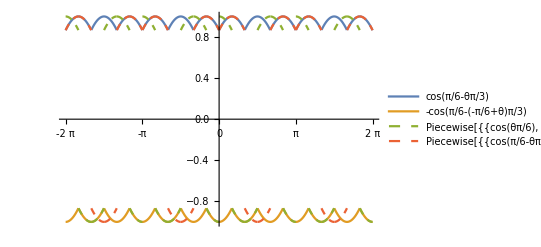

```mathematica
Row[{"fR"[θ],"=", ApplyToPiecewise[mForm,fSO[fSe[θ1],θ]],"⊗",ApplyToPiecewise[mForm,fRO[fRm[θ1,"fRe"],θ]]}]
Plot[Evaluate[{Cos[Mod[θ,Pi/3]-Pi/6],- Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],ApplyToPiecewise[#[[2]]&,fSO[fSe[Mod[θ,Pi/6]],θ]],ApplyToPiecewise[#[[3]]&,fSO[fSe[Mod[θ,Pi/6]],θ]]}],{θ,-2Pi,2Pi},Ticks->{PiTicks[-2Pi,2Pi],All},PlotLegends->"Expressions",PlotStyle->{Thick,Thick,Dashed,Dashed}]
```

Separate the sign from the piecewise function

```mathematica
fSs=Function[{θ},Piecewise[{{{1,1,1}, 0≤Mod[θ,π]<π/6}, {{1,-1,1}, π/6≤Mod[θ,π]<π/3}, {{1,-1,-1}, π/3≤Mod[θ,π]<π/2}, {{1,1,-1}, π/2≤Mod[θ,π]<(2 π)/3}, {{1,1,1}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1,-1,1}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]];

fSseDev=FullSimplify[Piecewise[{{{1,Cos[Mod[θ,π/6]],Cos[π/6-Mod[θ,π/6]]}, 0≤Mod[θ,π]<π/6}, {{1,Cos[π/6-Mod[θ,π/6]],Cos[Mod[θ,π/6]]}, π/6≤Mod[θ,π]<π/3}, {{1,Cos[Mod[θ,π/6]],Cos[π/6-Mod[θ,π/6]]}, π/3≤Mod[θ,π]<π/2}, {{1,Cos[π/6-Mod[θ,π/6]],Cos[Mod[θ,π/6]]}, π/2≤Mod[θ,π]<(2 π)/3}, {{1,Cos[Mod[θ,π/6]],Cos[π/6-Mod[θ,π/6]]}, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {{1,Cos[π/6-Mod[θ,π/6]],Cos[Mod[θ,π/6]]}, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]];
```

```mathematica
Row[{"fS"[θ],"=", ApplyToPiecewise[mForm,fSs[θ]],"⊗",ApplyToPiecewise[mForm,fSseDev]}]
```

fS[θ]=Piecewise[{{1
1
1, 0≤Mod[θ,π]<π/6}, {1
-1
1, π/6≤Mod[θ,π]<π/3}, {1
-1
-1, π/3≤Mod[θ,π]<π/2}, {1
1
-1, π/2≤Mod[θ,π]<(2 π)/3}, {1
1
1, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-1
1, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]⊗Piecewise[{{1
cos(π/6 - TemplateBox[List[
cos(TemplateBox[List[, π/6≤Mod[θ,π]<π/3||π/2≤Mod[θ,π]<(2 π)/3||(5 π)/6≤Mod[θ,π]<π}, {1
cos(TemplateBox[List[
cos(π/6 - TemplateBox[List[, 0≤Mod[θ,π]<π/6||π/3≤Mod[θ,π]<π/2||(2 π)/3≤Mod[θ,π]<(5 π)/6}, {0, True}}]

The Functions can be combined

```mathematica
Clear[fSse];fSse=Function[{θ},{1,Cos[Mod[θ-Pi/6,Pi/3]-Pi/6],Cos[Mod[θ,Pi/3]-Pi/6]}];
Row[{"fSe"[θ],"=",MatrixForm[fSse[θ]], "=",ApplyToPiecewise[MatrixForm,fSseDev]}]
```

fSe[θ]=(1
Cos[π/6-Mod[-π/6+θ,π/3]]
Cos[π/6-Mod[θ,π/3]])=Piecewise[{{(1
Cos[π/6-Mod[θ,π/6]]
Cos[Mod[θ,π/6]]), π/6≤Mod[θ,π]<π/3||π/2≤Mod[θ,π]<(2 π)/3||(5 π)/6≤Mod[θ,π]<π}, {(1
Cos[Mod[θ,π/6]]
Cos[π/6-Mod[θ,π/6]]), 0≤Mod[θ,π]<π/6||π/3≤Mod[θ,π]<π/2||(2 π)/3≤Mod[θ,π]<(5 π)/6}, {0, True}}]

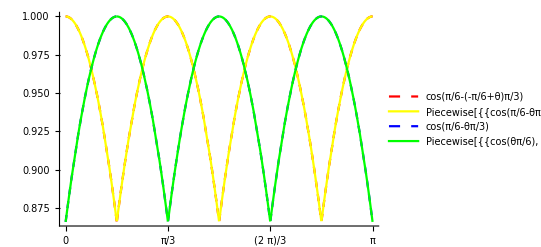

```mathematica
Plot[Evaluate[{fSse[θ][[2]],ApplyToPiecewise[#[[2]]&,fSseDev],fSse[θ][[3]],ApplyToPiecewise[#[[3]]&,fSseDev]}],{θ,0,Pi},Ticks->{PiTicks[0,Pi],All},PlotLegends->"Expressions",PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]}]
```

```mathematica
Row[{ApplyToPiecewise[mForm,fSO[fSe[θ1],θ]],"=", ApplyToPiecewise[mForm,fSse[θ]],"⊗",ApplyToPiecewise[mForm,fSs[θ]]}]
```

Piecewise[{{1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), π/6≤Mod[θ,π]<π/3}, {1
-cos(TraditionalForm`θ_1)
-cos(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - TraditionalForm`θ_1)
-cos(TraditionalForm`θ_1), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]=1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[⊗Piecewise[{{1
1
1, 0≤Mod[θ,π]<π/6}, {1
-1
1, π/6≤Mod[θ,π]<π/3}, {1
-1
-1, π/3≤Mod[θ,π]<π/2}, {1
1
-1, π/2≤Mod[θ,π]<(2 π)/3}, {1
1
1, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-1
1, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

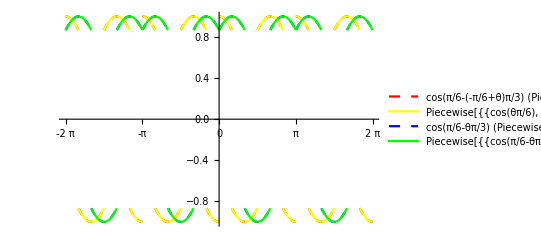

```mathematica
Plot[Evaluate[{fSse[θ][[2]] ApplyToPiecewise[#[[2]]&,fSs[θ]],ApplyToPiecewise[#[[2]]&,fSO[fSe[Mod[θ,Pi/6]],θ]],fSse[θ][[3]] ApplyToPiecewise[#[[3]]&,fSs[θ]],ApplyToPiecewise[#[[3]]&,fSO[fSe[Mod[θ,Pi/6]],θ]]}],{θ,-2Pi,2Pi},Ticks->{PiTicks[-2Pi,2Pi],All},PlotLegends->"Expressions",PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]}]
```

One further simplification if needed.

```mathematica
fSoo=Function[{θ},Piecewise[{{{1,1,1}, 0≤Mod[θ,2π/3]<π/6}, {{1,-1,1}, π/6≤Mod[θ,2π/3]<π/3}, {{1,-1,-1}, π/3≤Mod[θ,2π/3]<π/2}, {{1,1,-1}, π/2≤Mod[θ,2π/3]<(2 π)/3}, {0, True}}]];
fSo=Function[{θ},Piecewise[{{{1,1,1}, 0≤Mod[θ,2Pi]<π}, {{1,-1,-1}, π≤Mod[θ,2Pi]<2 π}, {0, True}}]];
```

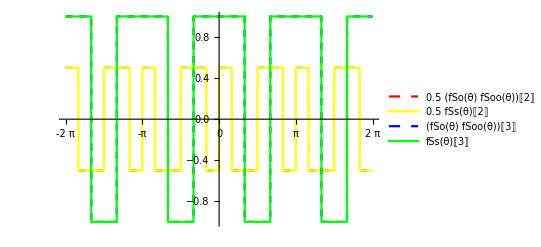

```mathematica
Plot[{0.5(fSo[θ]fSoo[θ])[[2]],0.5 fSs[θ][[2]],(fSo[θ]fSoo[θ])[[3]],fSs[θ][[3]]},{θ,-2Pi,2Pi},PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]},PlotLegends->"Expressions",Ticks->{PiTicks[-2Pi,2Pi],All}]
```

```mathematica
Row[{ApplyToPiecewise[mForm,fSO[fSe[θ1],θ]],"=", ApplyToPiecewise[mForm,fSse[θ]],"⊗",ApplyToPiecewise[mForm,fSo[θ]],"⊗",ApplyToPiecewise[mForm,fSoo[θ]]}]
```

Piecewise[{{1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), 0≤Mod[θ,π]<π/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), π/6≤Mod[θ,π]<π/3}, {1
-cos(TraditionalForm`θ_1)
-cos(π/6 - TraditionalForm`θ_1), π/3≤Mod[θ,π]<π/2}, {1
cos(π/6 - TraditionalForm`θ_1)
-cos(TraditionalForm`θ_1), π/2≤Mod[θ,π]<(2 π)/3}, {1
cos(TraditionalForm`θ_1)
cos(π/6 - TraditionalForm`θ_1), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-cos(π/6 - TraditionalForm`θ_1)
cos(TraditionalForm`θ_1), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]=1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[⊗Piecewise[{{1
1
1, 0≤Mod[θ,2 π]<π}, {1
-1
-1, π≤Mod[θ,2 π]<2 π}, {0, True}}]⊗Piecewise[{{1
1
1, 0≤Mod[θ,(2 π)/3]<π/6}, {1
-1
1, π/6≤Mod[θ,(2 π)/3]<π/3}, {1
-1
-1, π/3≤Mod[θ,(2 π)/3]<π/2}, {1
1
-1, π/2≤Mod[θ,(2 π)/3]<(2 π)/3}, {0, True}}]

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,1,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,1,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,2,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,2,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,3,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,3,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,4,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,4,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,5,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,5,1]]]},
{mForm[fSse[θ]] ,mForm[fSs[θ][[1,6,1]]],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fSe[θ]",FontWeight->Bold],"⊗"}],Row[{Style["fSs[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The Factored Rotation in each π/6 Region
-Graphics- | Scale : fSe[θ]⊗ | fSs[θ] | Factored Rotation : fR[θ]
A | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
1
1 | (1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1)
B | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
-1
1 | (1 | 1 | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1
-fRe(θ_1)-1 | fRe(θ_1) | 1)
C | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
-1
-1 | (1 | 1 | 1
1 | -fRe(θ_1)-1 | fRe(θ_1)
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1))
D | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
1
-1 | (1 | 1 | 1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1)
E | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
1
1 | (1 | 1 | 1
-fRe(θ_1)-1 | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1)
F | 1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ | 1
-1
1 | (1 | 1 | 1
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)
1 | -fRe(θ_1)-1 | fRe(θ_1))

```mathematica
lbls=Map[Style[#,FontSize->Large]&,{"A","B","C","D","E","F"}];
Row[{Column[{Text[Style["The Factored Rotation in each π/6 Region",FontSize->Large]],
partShow[Piecewise[{{lbls[[1]],Inequality[0,LessEqual,θ,Less,Pi/6]||Inequality[Pi,LessEqual,θ,Less,(7*Pi)/6]},{lbls[[2]],Inequality[Pi/6,LessEqual,θ,Less,Pi/3]||Inequality[(7*Pi)/6,LessEqual,θ,Less,(4*Pi)/3]},{lbls[[3]],Inequality[Pi/3,LessEqual,θ,Less,Pi/2]||Inequality[(4*Pi)/3,LessEqual,θ,Less,(3*Pi)/2]},{lbls[[4]],Inequality[Pi/2,LessEqual,θ,Less,(2*Pi)/3]||Inequality[(3*Pi)/2,LessEqual,θ,Less,(5*Pi)/3]},{lbls[[5]],Inequality[(2*Pi)/3,LessEqual,θ,Less,(5*Pi)/6]||Inequality[(5*Pi)/3,LessEqual,θ,Less,(11*Pi)/6]},{lbls[[6]],Inequality[(5*Pi)/6,LessEqual,θ,Less,Pi]||Inequality[(11*Pi)/6,LessEqual,θ,Less,2*Pi]}},0]]}],
TableForm[{
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,1,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,1,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,2,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,2,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,3,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,3,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,4,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,4,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,5,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,5,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,6,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fSe[θ]",FontWeight->Bold],"⊗",Style["fSs[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ] = fRO[fRm[θ1,fRe],θ]",FontWeight->Bold]}]}},TableAlignments->Center]}]
```

The Factored Rotation in each π/6 Region
-Graphics- | Scale : fSe[θ]⊗fSs[θ] | Factored Rotation : fR[θ] = fRO[fRm[θ1,fRe],θ]
A | fSe[θ]⊗1
1
1 | (1 | 1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1)
B | fSe[θ]⊗1
-1
1 | (1 | 1 | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1
-fRe(θ_1)-1 | fRe(θ_1) | 1)
C | fSe[θ]⊗1
-1
-1 | (1 | 1 | 1
1 | -fRe(θ_1)-1 | fRe(θ_1)
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1))
D | fSe[θ]⊗1
1
-1 | (1 | 1 | 1
fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1 | 1
fRe(θ_1) | 1 | -fRe(θ_1)-1)
E | fSe[θ]⊗1
1
1 | (1 | 1 | 1
-fRe(θ_1)-1 | fRe(θ_1) | 1
1 | fRe(π/6-θ_1) | -fRe(π/6-θ_1)-1)
F | fSe[θ]⊗1
-1
1 | (1 | 1 | 1
-fRe(π/6-θ_1)-1 | 1 | fRe(π/6-θ_1)
1 | -fRe(θ_1)-1 | fRe(θ_1))

```mathematica
TeXForm[TableForm[{
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,1,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,1,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,2,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,2,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,3,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,3,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,4,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,4,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,5,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,5,1]]]},
{Row[{Style["fSe[θ]",FontWeight->Bold],"⊗" ,mForm[fSs[θ][[1,6,1]]]}],TraditionalForm[fRO[fRm[θ1,"fRe"],θ][[1,6,1]]]}},TableHeadings->{lbls,{Row[{"Scale : ",Style["fSe[θ]",FontWeight->Bold],"⊗",Style["fSs[θ]",FontWeight->Bold]}],Row[{"Factored Rotation : ",Style["fR[θ] = fRO[fRm[θ1,fRe],θ]",FontWeight->Bold]}]}},TableAlignments->Center]]
```

\begin{array}{ccc}
  &  &  \\
 \text{A} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}(\delta \theta ) & 1 & \text{fRe}(-\delta \theta ) \\
 \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 \\
\end{array}
\right) \\
 \text{B} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) \\
 \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) & 1 \\
\end{array}
\right) \\
 \text{C} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 1 & \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) \\
 \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) \\
\end{array}
\right) \\
 \text{D} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 \\
 \text{fRe}(\delta \theta ) & 1 & \text{fRe}(-\delta \theta ) \\
\end{array}
\right) \\
 \text{E} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) & 1 \\
 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) & \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) \\
\end{array}
\right) \\
 \text{F} &  & \left(
\begin{array}{ccc}
 1 & 1 & 1 \\
 \text{fRe}\left(\delta \theta -\frac{\pi }{6}\right) & 1 & \text{fRe}\left(\frac{\pi }{6}-\delta \theta \right) \\
 1 & \text{fRe}(-\delta \theta ) & \text{fRe}(\delta \theta ) \\
\end{array}
\right) \\
\end{array}

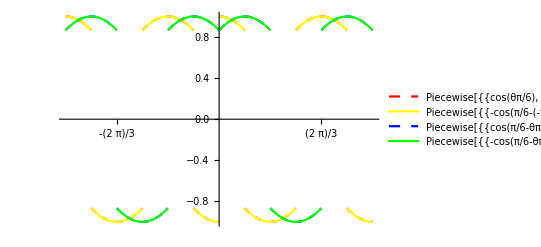

```mathematica
Clear[f,g]
Block[{f,g},
f=Function[{θ},Evaluate[fSO[fSe[Mod[θ,π/6]],θ]]];
fa=Function[{θ},Evaluate[ApplyToPiecewise[#[[2]]&,f[θ]]]];
fb=Function[{θ},Evaluate[ApplyToPiecewise[#[[3]]&,f[θ]]]];

g=Function[{θ},Evaluate[Assuming[Element[θ,Reals],ApplyToPiecewise[(fSse[θ]#)&,PiecewiseExpand[fSo[θ] fSoo[θ]]]]]];
ga=Function[{θ},Evaluate[ApplyToPiecewise[#[[2]]&,g[θ]]]];
gb=Function[{θ},Evaluate[ApplyToPiecewise[#[[3]]&,g[θ]]]];

Plot[Evaluate[{fa[θ],ga[θ],fb[θ],gb[θ]}],{θ,-Pi,Pi},PlotRange->{{-Pi,Pi},{-1,1}},PlotStyle->{Directive[Red,Thick,Dashed],Directive[Yellow,Normal],Directive[Blue,Thick,Dashed],Directive[Green,Normal]},Ticks->{PiTicks[-2Pi,2Pi],All},PlotLegends->"Expressions"]
]
```

then

```mathematica
Row[{TraditionalForm[scale["rR","fR"]["θ"]]," = ",TraditionalForm[fSs["θ"]]," ⊗ ",TraditionalForm[fSse["θ"]]}]
```

fS(θ) = fSs(θ) ⊗ fSse(θ)

, where  fSs(θ) is a piecewise function containing the signs.

```mathematica
Row[{ShowFun[fSs[θ]],"   and   ",ShowFun[fSse[θ]]}]
```

fSs(θ) = Piecewise[{{{1,1,1}, 0≤θπ<π/6}, {{1,-1,1}, π/6≤θπ<π/3}, {{1,-1,-1}, π/3≤θπ<π/2}, {{1,1,-1}, π/2≤θπ<(2 π)/3}, {{1,1,1}, (2 π)/3≤θπ<(5 π)/6}, {{1,-1,1}, (5 π)/6≤θπ<π}}]   and   fSse(θ) = {1,cos(π/6-(θ-π/6)π/3),cos(π/6-θπ/3)}

The scaling factors combine in a simple way

```mathematica
scale["nLCaCb","gR"]=scale["nLCaCb","LCaCb"][θ] scale["LCaCb","rR"][θ]fSse[θ];
Row[{"nR"[θ]," = ","nS"[θ]," ⊗ ","rS"," ⊗ ","fSse"[θ]," ⊗ ","fSs"[θ]," ⊗ ","fRO"["fRm"[θ1,"fRe"],θ]}]
Row[{"S"[θ]," = ","nS"[θ]," ⊗ ","rS"," ⊗ ","fSse"[θ]," = ",ApplyToPiecewise[mForm,scale["nLCaCb","LCaCb"][θ]],"⊗",mForm[scale["LCaCb","rR"][θ]],"⊗",ApplyToPiecewise[mForm,fSse[θ]]," = ",mForm[scale["nLCaCb","gR"]]}]
Row[{"nR"[θ]," = ","S"[θ]," ⊗ ","fSs"[θ]," ⊗ ","fRO"["fRm"[θ1,"fRe"],θ]}]
```

nR[θ] = nS[θ] ⊗ rS ⊗ fSse[θ] ⊗ fSs[θ] ⊗ fRO[fRm[θ1,fRe],θ]

S[θ] = nS[θ] ⊗ rS ⊗ fSse[θ] = ( TagBox[GridBox[{{1/√3}, {1/2 √3/2 sec(π/6 - TemplateBox[List[RowBox[List[⊗( TagBox[GridBox[{{1/√3}, {√2/3}, {√2/3}}, RowSpacings -> 1, ColumnAlignments -> Center, ColumnAlignments -> Left], Column] )⊗1
cos(π/6 - TemplateBox[List[RowBox[List[
cos(π/6 - TemplateBox[List[ = ( TagBox[GridBox[{{1/3}, {1/2}, {1/2}}, ColumnAlignments -> Center, RowSpacings -> 1, ColumnAlignments -> Left], Column] )

nR[θ] = S[θ] ⊗ fSs[θ] ⊗ fRO[fRm[θ1,fRe],θ]

The fully factorized matrix can now be written as

```mathematica
"nR"[θ]" = ""S"[θ]" ⊗ ""fSs"[θ]" ⊗ ""fRO"["fRm"[θ1,"fRe"],θ]
```

nR[θ] = S[θ] ⊗ fSs[θ] ⊗ fRO[fRm[θ1,fRe],θ]

```mathematica
TableForm[{
{"nR"[θ]," = ","S"[θ]," ⊗ ","fSs"[θ]," ⊗ ","fRO"["fRm"[θ1,"fRe"],θ]},
{"nR"[θ]," = ","S"[θ]," ⊗ ","fSs"[θ]," ⊗ ",mForm["fRO"[fRm[θ1,"fRe"],θ]]},
{"nR"[θ]," = ","S"[θ]," ⊗ ",ApplyToPiecewise[mForm,fSs[θ]]," ⊗ ",ApplyToPiecewise[mForm,fRO[fRm[θ1,"fRe"],θ]]},
}]
```

nR[θ] |  =  | S[θ] |  ⊗  | fSs[θ] |  ⊗  | fRO[fRm[θ1,fRe],θ]
nR[θ] |  =  | S[θ] |  ⊗  | fSs[θ] |  ⊗  | mForm[fRO[{{1,1,1},{fRe[θ1],1,-1-fRe[θ1]},{fRe[π/6-θ1],-1-fRe[π/6-θ1],1}},θ]]
nR[θ] |  =  | S[θ] |  ⊗  | Piecewise[{{1
1
1, 0≤Mod[θ,π]<π/6}, {1
-1
1, π/6≤Mod[θ,π]<π/3}, {1
-1
-1, π/3≤Mod[θ,π]<π/2}, {1
1
-1, π/2≤Mod[θ,π]<(2 π)/3}, {1
1
1, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1
-1
1, (5 π)/6≤Mod[θ,π]<π}, {0, True}}] |  ⊗  | Piecewise[{{1 | 1 | 1
fRe | 1 | -
fRe | - | 1, 0≤Mod[θ,π]<π/6}, {1 | 1 | 1
1 | fRe | -
- | fRe | 1, π/6≤Mod[θ,π]<π/3}, {1 | 1 | 1
1 | - | fRe
- | 1 | fRe, π/3≤Mod[θ,π]<π/2}, {1 | 1 | 1
fRe | - | 1
fRe | 1 | -, π/2≤Mod[θ,π]<(2 π)/3}, {1 | 1 | 1
- | fRe | 1
1 | fRe | -, (2 π)/3≤Mod[θ,π]<(5 π)/6}, {1 | 1 | 1
- | 1 | fRe
1 | - | fRe, (5 π)/6≤Mod[θ,π]<π}, {0, True}}]
Null |  |  |  |  |  |

```mathematica
Clear[gR,f];
gR=Function[{θ1,θ,f},Evaluate[Piecewise[Table[{Row[{MatrixForm[fSs[θ][[1,i,1]]]," ⊗ ",MatrixForm[fRO[fRm[θ1,f],θ][[1,i,1]]]}],fSs[θ][[1,i,2]]},{i,1,6}]]]];
Row[{"nR"[θ]," = ",mForm[scale["nLCaCb","gR"]]," ⊗ ",gR[θ1,θ,"fRe"]}]
```

nR[θ] = ( TagBox[GridBox[{{1/3}, {1/2}, {1/2}}, ColumnAlignments -> Center, RowSpacings -> 1, ColumnAlignments -> Left], Column] ) ⊗ Piecewise[{{(1
1
1) ⊗ (1 | 1 | 1
fRe[θ1] | 1 | -1-fRe[θ1]
fRe[π/6-θ1] | -1-fRe[π/6-θ1] | 1), 0≤Mod[θ,π]<π/6}, {(1
-1
1) ⊗ (1 | 1 | 1
1 | fRe[π/6-θ1] | -1-fRe[π/6-θ1]
-1-fRe[θ1] | fRe[θ1] | 1), π/6≤Mod[θ,π]<π/3}, {(1
-1
-1) ⊗ (1 | 1 | 1
1 | -1-fRe[θ1] | fRe[θ1]
-1-fRe[π/6-θ1] | 1 | fRe[π/6-θ1]), π/3≤Mod[θ,π]<π/2}, {(1
1
-1) ⊗ (1 | 1 | 1
fRe[π/6-θ1] | -1-fRe[π/6-θ1] | 1
fRe[θ1] | 1 | -1-fRe[θ1]), π/2≤Mod[θ,π]<(2 π)/3}, {(1
1
1) ⊗ (1 | 1 | 1
-1-fRe[θ1] | fRe[θ1] | 1
1 | fRe[π/6-θ1] | -1-fRe[π/6-θ1]), (2 π)/3≤Mod[θ,π]<(5 π)/6}, {(1
-1
1) ⊗ (1 | 1 | 1
-1-fRe[π/6-θ1] | 1 | fRe[π/6-θ1]
1 | -1-fRe[θ1] | fRe[θ1]), (5 π)/6≤Mod[θ,π]<π}, {0, True}}]

#### Quantizing the Rotation

The factored rotation fR contains 4 non-integer elements lying between -1 and 0, which we wish to quantize. This can be done simply by multiplying it by 2^(n-2), where n is the bit depth of the integer type, and rounding the result:

```mathematica
Row[{qR["θ"]," = ",fRO[qRm["θ_1","fRe",n],"θ_6"],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]
Row[{ShowFun[qR[θ6,θ1,"fRe",n]],"  where  ",Column[{Row[{ "fRe = ",fRe[θ]}],Row[{TraditionalForm[θ1]," = ",TraditionalForm[Mod[θ,π/6]]}],Row[{TraditionalForm[θ6]," = ",TraditionalForm[Mod[θ,π]]}]}]}]
Row[{"qRm = ",TraditionalForm[mForm[qRmFun[θ1,"fRe",n]]]}]
```

qR[θ] = fRO[qRm[θ_1,fRe,n],θ_6]  where  fRe = 1/2 (-1-√3 Tan[θ])
θ_1 = θπ/6
θ_6 = θπ

qR(θ6,θ1,fRe,n) = Piecewise[{{(1 | 1 | 1
Round[2^(n-2) fRe(θ_1)] | 2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2)
Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2)), 0≤θ_6<π/6}, {(1 | 1 | 1
2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2)
-Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)] | 2^(n-2)), π/6≤θ_6<π/3}, {(1 | 1 | 1
2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)]
-Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)]), π/3≤θ_6<π/2}, {(1 | 1 | 1
Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2)
Round[2^(n-2) fRe(θ_1)] | 2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2)), π/2≤θ_6<(2 π)/3}, {(1 | 1 | 1
-Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)] | 2^(n-2)
2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)] | -Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2)), (2 π)/3≤θ_6<(5 π)/6}, {(1 | 1 | 1
-Round[2^(n-2) fRe(π/6-θ_1)]-2^(n-2) | 2^(n-2) | Round[2^(n-2) fRe(π/6-θ_1)]
2^(n-2) | -Round[2^(n-2) fRe(θ_1)]-2^(n-2) | Round[2^(n-2) fRe(θ_1)]), (5 π)/6≤θ_6<π}}]  where  fRe = 1/2 (-1-√3 Tan[θ])
θ_1 = θπ/6
θ_6 = θπ

qRm = 1 | 1 | 1
Round[2^n - 2  | 2^n - 2 | -Round[2^n - 2 
Round[2^n - 2  | -Round[2^n - 2  | 2^n - 2

Since every row in  fR always has an element equal to 1, we will exploit the full range (-2)^(n-2)≤fR≤2^(n-2) of the integer type.

```mathematica
Style[TraditionalForm[Row[{fR["θ"]," = ",scale["fR","qR"]⊗(qR["θ"]+δqR["θ"])}]],Larger]
Style[TraditionalForm[Row[{nLCaCb["θ"]," = ",scale["nLCaCb","LCaCb"]["θ"] ⊗ scale["LCaCb","rR"]["θ"] ⊗ scale["rR","fRs"]["θ"] ⊗ fSs["θ"] ⊗ scale["fR","qR"]⊗(qR["θ"]+δqR["θ"])}]],Larger]
```

fR(θ) = qS⊗(qR(θ)+δqR(θ))

nR(θ) = L^-1(θ)⊗rS⊗fSse(θ)⊗fSs(θ)⊗qS⊗(qR(θ)+δqR(θ))

Thus far, we have assumed that we can achieve a bit depth of two less than the bit depth of the source type for the representation of the rotation matrix. We are now in a position to assess whether the representation introduces any errors.

Given that the source type with a bit depth of n, we can work out any errors introduced by finding the difference between using the quantized rotation  and the unquantized rotation . All the factoring of the rotation is mathematically exact up to and including , so any errors that are introduced will be during the rounding.

We are interested in the error introduced by the quantization, so we introduce the perturbation [θ] associated with the transform [θ] produced by the rounding. Defining

```mathematica
Style[TraditionalForm[Row[{fRe["θ"]," = ",scale["fR","qR"]⊗(qRe["θ"]+δqRe["θ"])}]],Larger]
```

fRe(θ) = qS⊗(qRe(θ)+δqRe(θ))

[θ]  |  ==[n]⊗([θ,n]+[θ,n])

because  has equal elements in the second and third rows

```mathematica
Style[TraditionalForm[Row[{fRO[scale["fR","qR"]⊗ Style["A",Bold],θ6]," = ",scale["fR","qR"]⊗fRO[ Style["A",Bold],θ6]}]],Larger]
```

fRO(qS⊗A,θ_6) = qS⊗fRO(A,θ_6)

then

[θ]  |  ==[[θ]] 
   |  ==[[n]⊗([θ,n]+[θ,n])] 
   |  ==[n]⊗[[θ,n]+[θ,n]] 
   |  ==[n]⊗[[θ,n]]+[n]⊗[[θ,n]]

The perturbation depends entirely on [θ,n]

[ϕ]  |  ==Round[2^(n-2)[ϕ]]-2^(n-2)[ϕ] 
   |  ==Round[2^(n-3)√3 tan(ϕ)]-2^(n-3)√3 tan(ϕ) 
 [ϕ]  |  ==2^(2-n)[ϕ]

The perturbation [θ] is a rearrangement of []  
{{Cell[TextData[{" ", Cell[BoxData[FormBox[RowBox[{"[", "]"}], TraditionalForm]], "InlineFormula"], " "}]], Cell[TextData[{" ", Cell[BoxData[FormBox[RowBox[{"==", RowBox[{"[", ",", "]"}]}], TraditionalForm]], "InlineFormula"], " "}]]}, {Cell[TextData[{" ", Cell[BoxData[FormBox["", TraditionalForm]], "InlineFormula"], " "}]], Cell[TextData[{" ", Cell[BoxData[FormBox[RowBox[{"==", "(", Cell[BoxData[FormBox[GridBox[{{Cell[TextData[{" ", Cell["0", "InlineFormula"], " "}]], Cell[TextData[{" ", Cell["0", "InlineFormula"], " "}]], Cell[TextData[{" ", Cell["0", "InlineFormula"], " "}]]}, {Cell[TextData[{" ", Cell[RowBox[{"[", "]"}], "InlineFormula"], " "}]], Cell[TextData[{" ", Cell["0", "InlineFormula"], " "}]], Cell[TextData[{" ", Cell[RowBox[{"[", "-", "]"}], "InlineFormula"], " "}]]}, {Cell[TextData[{" ", Cell[RowBox[{"[", "6-", "]"}], "InlineFormula"], " "}]], Cell[TextData[{" ", Cell[RowBox[{"[", "-6", "]"}], "InlineFormula"], " "}]], Cell[TextData[{" ", Cell["0", "InlineFormula"], " "}]]}}], TraditionalForm]]], ")"}], TraditionalForm]], "InlineFormula"], " "}]]}}

The perturbation introduced to each channel is further simplified by recognizing that [-ϕ]==-1-[ϕ], which allows us to find [-ϕ]==-[ϕ] i.e. that the sum of the two perturbations in each row equals zero. we can analyze the quantization error in terms of just one function  and a matrix ordering function [θ]==[[]].

[θ]  |  ==[( 0 
 [
] 
 [
6-
] )⊗( 0  |  0  |  0 
 1  |  0  |  -1 
 1  |  -1  |  0 ),θ] 
   |  ==[( 0 
 [
] 
 [
6-
] )]⊗[θ]

where

[( 0 
 a 
 b ),θ]=={ ( 0 
 a 
 b )  |  0≤(θmod π/3)<π/6 
 ( 0 
 b 
 a )  |  π/6≤(θmod π/3)<π/3

[θ]=={ ( 0  |  0  |  0 
 1  |  0  |  -1 
 1  |  -1  |  0 )  |  0≤(θmodπ)<π/6 
 ( 0  |  0  |  0 
 0  |  1  |  -1 
 -1  |  1  |  0 )  |  π/6≤(θmodπ)<π/3 
 ( 0  |  0  |  0 
 0  |  -1  |  1 
 -1  |  0  |  1 )  |  π/3≤(θmodπ)<π/2 
 ( 0  |  0  |  0 
 1  |  -1  |  0 
 1  |  0  |  -1 )  |  π/2≤(θmodπ)<(2π)/3 
 ( 0  |  0  |  0 
 -1  |  1  |  0 
 0  |  1  |  -1 )  |  (2π)/3≤(θmodπ)<(5π)/6 
 ( 0  |  0  |  0 
 -1  |  0  |  1 
 0  |  -1  |  1 )  |  (5π)/6≤(θmodπ)<π

We can now express the perturbation to the rotation and to the channel elements themselves. The structure of  means that the perturbation to each channel is the product of either [] or [6-] with the difference between two of the pixel values. Given that we can assume that the pixel values are positive, being unsigned integers, the extreme values of the perturbation are when one of the two pixel values is zero.

[θ]  |  ==[θ]+[θ] 
   |  ==[θ]⊗⊗(θ)⊗[n]⊗[θ]⊗[[θ,n]+[θ,n]] 
   |  ==( 1 
 1 
 1 )⊗( 1 
 2 
 2 )⊗(θ)⊗[[θ,n]+[θ,n]]

defining

[θ,n]  |  ==( 1 
 2 
 2 )⊗(θ) 
 [θ]  |  ==[θ]⊗[[θ,n]] 
 [θ]  |  ==[θ]⊗[[θ,n]]

the perturbation to the rotated channel elements  is found for an input set of pixel values ==2^n

+  |  ==[θ]·+[θ]· 
   |  ==2^n[θ]· 
   |  ==2^n[θ]⊗[[θ,n]]· 
   |  ==[( 0 
 2
[] 
 2
[6-] )⊗( 0  |  0  |  0 
 1  |  0  |  -1 
 1  |  -1  |  0 ),θ]

So, to minimize the perturbation, we need to simultaneously minimize ±2[] and ±2[6-]

caption Perturbation to channels a and b against angle δθ 
For n == 8 with ι regions shaded and extrema labelled

The maxima for each function are where ±2[]==±1 and ±2[6-]==±1, and the minima are where ±2[]==0 and ±2[6-]==0. To find the corresponding values of , all that is needed is an inverse function for . In essence [ϕ] discretizes √3 tan(ϕ) into steps of 2^(3-n). The minima can be found by taking the inverse of √3 tan(ϕ), given that 0≤√3 tan(ϕ)≤1 for 0≤ϕ≤6 we can say that Round[2^(n-3)√3 tan(ϕ)]∈{0,1,2,⋯2^(n-3)}

[ϕ]  |  ==0  |  [6-ϕ]  |  ==0  when 
 2^(n-3)√3 tan(ϕ)  |  ==m  |  2^(n-3)√3 tan(6-ϕ)  |  ==m  where  m==0,1,2⋯2^(n-3) 
 b==  |  arctan((m 2^(3-n))/(√3))  |  a==  |  arctan((2 √3 m)/(2^n-2m))

The maxima can be found by recognizing that the maximum rounding error is a half and evaluating at these points

[b]  |  ==±1  |  [6-a]  |  ==±1  when 
 b  |  ==arctan(2^(3-n)/(√3)(m+1/2))  |  a  |  ==arctan((2 √3(m+1/2))/(2^n-2(m+1/2))) 
 b  |  ==arctan(((2m+1)2^(2-n))/(√3))  |  a  |  ==arctan((√3(2m+1))/(2^n-2m-1)) 
     |  with  m==0,1,2,3⋯2^(n-3)-1  |  |

We are interested in a compromise between the perturbations to each channel which is where the perturbations intersect. It would be useful to be able to assign a relative importance α and β to each channel a and b respectively.

β [ϕ]==α [π/6-ϕ]  when
 βRound[2^(n-3)√3 tan(ϕ)]-αRound[2^(n-3)√3 tan(π/6-ϕ)] 
 ==2^(n-3)(√3 αtan(θ)+2βsin(θ)sec(π/6-θ))

The values α and β can only move the point of intersection within the bounds of the extrema. Therefore, any solution for the point of intersection will enable the bounding extrema to be identified.

We solve first for the case where α==1 and β==1. Recognizing that the rounded part can only take certain values

i==Round[2^(n-3)√3 tan(ϕ)]-Round[2^(n-3)√3 tan(π/6-ϕ)]  where  i==0,1,2⋯2^(n-2)

then

i==arctan((√(i^2 2^(6-2n)-i 2^(4-n)+49)+i 2^(3-n)-7)/(2 √3))  where  i==0,1,2⋯2^(n-2)

Each point of intersection is defined and bounded by 4 extrema. Comparing with the functional form of the extrema allows these 4 points to be identified.

Separating the points of intersection into even and odd terms facilitates the identification.

|  Channel a   |  Channel b   |  i  
 Minima   |  a
(i/2)
==
a
i   |  b
(i/2)
==
b
i   |  i
∈
{0,2,4,6⋯2^(n-2)} 
 Maxima   |  a
((i-1)/2)
==
a
i   |  b
((i-1)/2)
==
b
i   |  i
∈
{1,3,5,7⋯2^(n-2)-1}

The following ranges are guaranteed to be true for even or odd values of i, with very specific values of p and q.

b
p-1 | <
a
q | <  |  i< | a
q+1
< | b
p  |  ⋁a
q+1 | <
b
p | <  |  i+1< | b
p+1
< | a
q+2  |  p | ∈
{2N}
q | ∈
{2N}
2 | ≤
i
≤
2^(n-2)
-
1

This slightly glib definition illustrates the pattern for the extrema bounding the points of intersection. At the start of a Π/6 region, i.e. for low values of i, p==i and q==i. The maxima swap orderings between certain values of i within a Π/6 region. This is evident in the inescapable indices of i-1 and i+1, regardless of the starting values for i for either the maxima or minima. So, whilst it is true that ai>bi, it is not always true that ai+1>bi-1. This leads to the question of what happens when this boundary ai+1==bi-1 is crossed. Firstly, the even-odd ordering (i.e. the a-b channel ordering) is flipped; secondly, the indices are shifted. A second transition restores the a-b ordering and shifts the indices again. As the index i passes the half way point ==2^(n-3), the transitions occur in the opposite direction, restoring the indices and ordering. Transitions occur where i satisfies ai+ι==bi-ι, with ι∈{1,2,3⋯(7-4 √3)2^(n-3)}.

==2^(n-3)    Γ(ι,n)==√(ι^2-14ι+^2)

The region ι for a given value of i is the highest value of ι for which the following condition remains true:

-Γ(ι,n)≤i≤Γ(ι,n)+

For a given value of θ and n, we can find the intersection index i, and from this we can find ι:

i(δθ,n)==(tan(δθ)(√3 tan(δθ)+7))/(tan(δθ)+√3)  where  δθ==θ  mod π/6
ι(i,n)==⌊7 -√(i^2-2i +49 2)⌋

The sequence of a-b channel extrema depends on both the index i and the region ι in the following way:

b
i-ι-1 | <
a
i+ι | <  |  i< | a
i+ι+1
< | b
i-ι  |  when  i
∈
{2N+1} | ⋀ | ι
∈
{2N+1}
 
⋁
i
∈
{2N} | ⋀ | ι
∈
{2N} 
 a
i+ι | <
b
i-ι-1 | <  |  i< | b
i-ι
< | a
i+ι+1  |  when  (
i∈{2N+1} | ⋀ | ι
∈
{2N}
) 
⋁
(
i∈{2N} | ⋀ | ι
∈
{2N+1}
)

We want to classify the points of intersection as greater or lesser than a tolerance 0<τ≤1. In order to do this, we make a linear approximation to the perturbation between the extrema. There is one point of intersection between each of the maxima and corresponding minima. A bit of geometry allows us to write a classification criteria for each of the points of intersection.

Defining a function for the degree of error at the point of intersection using the linear approximation from the four extrema surrounding the point, and generalizing to allow for different maximum errors α for channel a and β for channel b. The conditions on i and ι can be more compactly written by applying a condition to their product.

h(i,ι)=={ (αβ(ai+ι-bi-ι))/(β(ai+ι-ai+ι+1)+α(bi-ι-1-bi-ι))  |  i+ι∈{2N} 
 (αβ(bi-ι-1-ai+ι+1))/(β(ai+ι-ai+ι+1)+α(bi-ι-1-bi-ι))  |  i+ι∈{2N+1}

allows the criteria for a channel to be written as τ≥h(i,ι).

The criteria τ== with α==β selects from either the odd values or the even values of i, because if h(i,n)< is true, then h(i+1,n)< is false and vice versa. There are 2^(n-2) points of intersection and 2^(n-3) which satisfy the criteria τ==1/2. The algorithm as implemented in openCV leaves the decision about the criteria up to the programmer. The programmer chooses a value for θ and selects a value for τ. The algorithm returns the nearest value of θ which satisfies the condition defined by τ. The programmer then decides whether the suggested value for θ is acceptable and either adopts the suggested value, or chooses a value as close as possible, accepting the possibility of errors.

For example, in this project n is 8, so ∈{(-2)^(8-2)⋯2^(8-2)}, which gives 2^(8-3)-1 values in each π/6 region, producing a maximum perturbation of less than . In total, there are 12(2^(8-3)-1)==372 possible values for θ which produces a maximum perturbation of less than . This would allow the destination pixel values to be expressed in 8-bit numbers without error using a transformation matrix expressed in 6-bit signed integers. The statistics performed to determine θ are not demanding enough to justify rejecting a suggested value of theta within 1of the requested value. It is, however, important to know the value actually used in the algorithm, which is why the mechanism for adjusting θ is separate from the color-space algorithm and is under the control of the programmer. For instance, in the implementation below, the suggested value is accepted and used to adjust the statistical model, keeping all the values in correct correspondence.

## Preservation of Color Information

The goal of the algorithm is to preserve all the information captured by the camera which relates to skin whilst discarding as much of the irrelevant information as possible. Given that edges and features often present as shadows and highlights, all the information captured in terms of luminosity will be regarded as relevant information, at least as far as the manipulation of individual pixel values is concerned. Considering the chromatic information, the importance of the pixel value will be directly determined by a Gaussian distribution.

Knowing the range of values produced by the rotation allows us to scale the transformation to fit into the range of the destination data type. If we have RGB pixel values in a given machine data type, the amount of information contained in each of those channels is equal to the number of values accessible in that data type. For example: for 8-bit, unsigned integers, there are 256 possible values. After a rotation, we are interested in the amount of information which lies along the new axes. This is found simply by multiplying the range of the source data type by the length of the new axes found for the unit cube. To preserve all the information captured, we would therefore have to use a larger data type to store the new values. We are, however, only interested in a small region in the chromatic space. The question is, then, how to preserve the relevant information in a way consistent with the significance indicated by the aforementioned Gaussian distribution.

None of the rotated axes have lengths less than 1 for the unit RGB cube. For this reason we’ve written redistribution functions which perform any necessary type conversion whilst preserving the information in a controlled way; we can keep the information where it’s needed and discard it where it’s irrelevant. So although this is strictly beyond the normal meaning of a color space conversion, it is addressing a connected issue and belongs in the conversion. In terms of optimization, it is also the most efficient place in the code in which to perform this adjustment, allowing us to — for the sake of example — discard the details of the colors of a duck’s feathers whilst keeping the hues and tones of human skin.

We can use a function to redistribute the information contained on the longer axis onto the shorter axis, which can be expressed in the discrete representation of that axis necessitated by internal integer data types. There are three ways in which to implement the redistribution functions:

### Partition

The most straightforward redistribution method is to simply preserve the information in a 1-to-1 fashion within a region. The region can be defined in terms of the distribution Gaussian by specifying a significance level in terms of the variance or the standard deviation.

### Linear

A slightly more sophisticated method is to use a linear redistribution. A linear distribution is equivalent to partitioning given a unit gradient. However, a linear redistribution function allows for the possibility of data compression. So then, in the case where the region of interest contains more information than can be expressed in the destination data type, a linear distribution function allows an even compression of the information from source to destination.  Lee2002

### ERF (Gaussian Error Function)

The integral of the cumulative Gaussian (i.e. Error Function) allows the redistribution of the information on the axis in a way which selectively preserves the information about a point on the axis (i.e. the mean of the Gaussian), and then progressively discard the information as it falls into the tails of the Gaussian. So, it provides a non-linear distribution of the information. The Gaussian can be seen as describing our interest in the information contained along the axis, so it’s logical to use the error function to redistribute the information. The disadvantage of this is simply the computational effort involved in generating the error function.

The error function distribution is mathematically correct, being directly related to the Gaussian fit. Computationally, there are two considerations: the numerical representation, and performance. The discrete representation of the numerics means that — for a significant number of possible distributions — distributing using the error function has little to no advantage (or indeed difference) from using a linear distribution.

Considering the preservation of information captured, mappings with a gradient greater than 1 are undesirable because they preserve all the information whilst being informatically wasteful in that there are functionally inaccessible discrete values in the destination range. Our stated aim is to preserve the information in the image pertaining to human skin; unevenly distributing this information across a discrete data type is not only wasteful in terms of memory, but also of processing resources because subsequent processing routines will treat the data as if it has a higher fidelity than it actually does.

To construct a distribution function, we first need to describe the relationship of the error function to the Gaussian fit, and then produce a function with the appropriate range and domain. For a Gaussian fit with an amplitude A, a mean of μ, and a standard deviation of σ, where μ and x lie in a source range  from  to . The cumulative distribution is found by integrating from  to the point x, as can be seen in (Section ):

∫^x A(e^(-(t-μ)^2/(2 σ^2)))/(√(2π)σ)dt==1/2 A(erf((x-μ)/(√2 σ))-erf(-μ/(√2 σ)))

The Gaussian distribution and the cumulative distribution are shown in Figure Section  for some values chosen for illustrative purposes. All that is required now is to fix the range  to  for the domain  to .

First, we determine the maximum value taken in the domain. This is simply found by evaluating the function at . It should be noted that — if the Gaussian distribution is well contained in the source domain — the maximum value should be equal to the amplitude. For the sake of simplicity, we’ll ignore the amplitude of the fitted Gaussian found previously as it is not relevant to the design of the redistribution function. So, to fix the range of the distribution function, we first scale to the range 0:1 by simply dividing through by the maximum value, and then re-scale to the destination range ==- and shift by .

dis(x)==(()(erf((x-μ)/(√2 σ))-erf(-μ/(√2 σ))))/(erf(-μ/(√2 σ))-erf(-μ/(√2 σ)))+

### Efficiently Implementing the Distribution Function

Mathematically, the ERF distribution function (Section ) achieves all the stated objectives. However, on a device we are dealing with discrete numerics and limited processing power, so further analysis is required. Where we’re using a discrete domain and range, the distribution is usefully divided into three characteristic behaviours: where it is constant, where it preserves all the information, and where it selectively preserves information. Looking at the distribution, this divides the source domain into five regions: two where it is effectively constant, two where it is selective, and one region around the mean where it preserves all the information. In order to design an efficient algorithm, it is useful to identify the boundaries of these five regions.

#### The Region Which Discards All Information

First, we need to identify where the distribution is effectively constant. This can be found by solving the following equation in the region and domain 0≤x≤1 and then generalized to the specific discrete numerics:

(erf(μ/(√2 σ))+erf((x-μ)/(√2 σ)))/(erf(μ/(√2 σ))-erf((μ-1)/(√2 σ)))==dL  where  dL==

The solution is found for the source domain in the range 0:1 as:

x==√2 σ erf^-1((dL-1)erf(μ/(√2 σ))-dL erf((μ-1)/(√2 σ)))+μ

The boundaries of the regions x<_1 and x>_2 for x∈{⋯} or x<_1 and x>_2 for x∈{0⋯1} can be written using the following helpful constants of the distribution.

Σ^-  |  ==erf((μ-1)/(√2 σ))  |  Σ^+  |  ==erf(μ/(√2 σ))  |  dL  |  ==  |  κ  |  ==

_1  |  ==σ √2 erf^-1((dL-1)Σ^+-dL Σ^-)+μ  |  _2  |  ==σ √2 erf^-1((dL-1)Σ^--dL Σ^+)+μ 
 _1  |  ==+(_1(μ,σ))  |  _2  |  ==+(_2(μ,σ))

#### The Region Which Keeps All Information

To find the region where all the information in the source domain is preserved, we differentiate the distribution and solve for where the gradient is equal to the destination range over the source range. This corresponds to the point at which a unit change in the source produces a unit change in the destination range:

(√(2/π)e^(-(x-μ)^2/(2 σ^2)))/(σ(erf(μ/(√2 σ))-erf((μ-1)/(√2 σ))))==

Rearranging for x, we find:

x==μ±σ √(-2log(σ(erf(μ/(√2 σ))-erf((μ-1)/(√2 σ))))+2log()+log(2/π))

The boundaries of the region _1<x<_2 for x∈{⋯} and _1<x<_2 for x∈{0⋯1} can be written using the following helpful constants of the distribution.

Σ^-  |  ==erf((μ-1)/(√2 σ))  |  Σ^+  |  ==erf(μ/(√2 σ))  |  κ  |  ==

w(μ,σ)==σ √(log(2/π)-2log(κσ(Σ^+-Σ^-)))

The equations are found in the unit source domain 0:1. It is a simple matter to scale and shift these values to give the points in a more general source domain.

_1(μ,σ)  |  ==μ-w(μ,σ)  |  _2(μ,σ)  |  ==μ+w(μ,σ) 
 _1(μ,σ)  |  ==+(μ-w(μ,σ))  |  _2(μ,σ)  |  ==+(μ+w(μ,σ))

One refinement can be made to these values by recognizing that the discrete distribution extends the effectively linear region past the analytic solution by rounding the values. This can be seen in Section , where the shaded squares are the rounded values. The extended region boundary  was found by numerically solving

⌊dis(_2)⌋+(x-_2)==dis(x)

In the C++ code, whilst numerical routines were used MatLab and Mathematica to perform the analysis, the extended region boundary point was found by ’walking’ along the distribution from the analytic point _2 until divergence from linear behaviour became apparent. This is regarded as a simpler solution, not requiring the use of numerical library routines, and proved to be a quick and elegant solution for the C++ implementation. The extended boundaries _1 and _2 are then defined by

⌈dis(_1)⌉-_1  |  ==dis(_1)-_1  |  ⌊dis(_2)⌋-_2  |  ==dis(_2)-_2

#### The compression ratio

There is one final value of interest to the development of the algorithm, which is the gradient at the mean. The reason this is of interest is because we’re trying to compress the relevant data as much as possible. If the destination region is small (i.e. the destination machine type is smaller than the source type), then the gradient at the mean allows us to assess the fidelity required of the source type. If it weren’t for the fact that the source is the result of a rotation transformation, then there would be little purpose in assessing this value. However, it is entirely possible that the lengthening of the axes resulting from the rotation is insignificant for the desired destination type; there’s no point preserving information during the rotation which is then discarded by the redistribution. The gradient is given by

The compression ratio is at most one-to-one, therefore κ<==1 and the gradient in the unit space must always be greater than one 1≤δ(μ,σ). so κ≤Δ(μ,σ)≤δ(μ,σ).

The required fidelity in the source domain can be found using Δ in the sense that the correspondence between one information step in the source must produce a step of Δ in the destination type. For the algorithm evaluating the maximum gradient Δ allows us to be sure that  — the region on the x axis where all the information is to be preserved — exists if Δ>1 or tells us that the x axis can be shortened if Δ<1. In the algorithm Δ is used to find an appropriate working data type for the rotated color space and to define the axis scaling for the rotation matrix.

We need to consider the requested compression of information alongside the spread of information caused by the rotation, and the desired focus on the specific region of interest dictated by the statistics. Each axis in the color space is to be represented by a discrete set of numbers. The size of these sets dictates the discretization of the axis, and the ratios between them indicates the spread or compression of the information they contain. We assume that the RGB axes are each discretized to the same extent, each containing  values. After the application of the un-normalized rotational transformation, the axes contain differing numbers of values given by _1== √3, _2== L_2(θ) and _3== L_3(θ). These axis lengths preserve all the information contained in the source color space, and so are the maximum length the axis should take. The minumum length the axis may take is where the information is lost evenly throuought the axis, and corresponds to an axis length equal to the destination axis length ==.

We can now write an algorithm which determines the necessary scaling for the axes, and whether truncation of the extreme values is significant. As this will alter  we fix the values of κ and Δ to be those for the working range ==L(θ) which preserves all information. With this value the constants are

The length of the axis  after rescaling should be

(θ,μ,σ)  |  ==min{K/(L(θ))δ(μ,σ),1}L(θ) 
   |  ==min{Kδ(μ,σ),L(θ)}

The scaling  comes from the source pixel values, the remaining terms translates simply into a rotation matrix scaling

This satisfies the requirements placed on the gradient Δ(μ,σ)>1 because: if we substitute for  in the definition for the gradient Section

Δ(μ,σ)  |  ==max{K/(L(θ))δ(μ,σ),1}

And the compression ratio κ is also explicitly restricted to being at most one and now is no longer defined in terms of .

κ(θ)  |  ==max{1/(δ(μ,σ)),K/(L(θ))}

#### A Piecewise Approximation to the ERF Distribution

We now have equations which give us the four points in the source domain which mark the boundaries of the five characteristic regions. We can now use them to define a piecewise function which uses the computationally problematic error function based distribution as little as possible

pDis(x)=={   |  x≤_1 
 dis(x)  |  _1<x<_1 
 x-_1+dis(_1)  |  _1≤x≤_2 
 dis(x)+_2-_1-dis(_2)+dis(_1)  |  _2<x<_2 
 dis(_2)+_2-_1-dis(_2)+dis(_1)  |  x≥_2

All three distribution techniques ( Section  , Section  , Section  ) described earlier are special cases of this distribution. When the distribution has a very large variance the piecewise distribution can be simplified as a linear distribution figSection . When the distribution has a very small variance a partitioning is more appropriate fig Section . The most interesting distributions, however, are the ones which require the use of the piecewise distribution fig Section .

## The Skin Color Space Algorithm

Now that all of the values necessary to preserve the skin information have been obtained, we can use them to build a color space transformation algorithm which can make intelligent decisions about the numerical precision for the intermediate and final variables, as well as determining the most efficient transformation methods. The algorithm described herein will take values of θ, the rotation about the luminosity axis, the standard deviations a,b and mean values a,b for the two chromatic axes in the unit range and will automatically decide upon the necessary intermediate working data types and the most efficient redistribution methods.

Previously, we found a rotational transformation which allows a working type  to be chosen such that ≤2. If we were to keep the same data type for the color space  as is used for the RGB values , then the axes would have to be rescaled with the accompanying loss of information. Given that we have values which allow us to assess where all the relevant information lies, a more sophisticated approach is possible. For a chromatic axis — which, after rotation, has a length L(θ) — we can determine the positions on that axis at which the information is considered irrelevant using Equation (Section ) and the positions where the information is all considered relevant. If the gradient Δ Section  is less than 1, then the distribution loses information at all points on the axis and the axis can be shortened without loss of relevant information. The only further consideration is to ensure that the values outside that range are prevented from causing errors associated with overflow. To exclude this possibility, a conditional statement can be used which checks the bounds as stated, assigning an appropriate value as necessary. The alternative is to use an intermediate value with a higher bit depth, and then to recast into the destination data type in such a way that overflow and underflow are handled appropriately. The OpenCV library provides a casting method — saturateCast — which serves this purpose.

#### Setting the Value for the Tolerance

Now that we have the working type range , accounting for both the rotation and the statistics, we can set a meaningful tolerance on the error. Previously we calculated that the maximum error would occur for pixel values at the corners of the RGB cube, we have now seen that some values are more important than others and that it is more meaningful to use a smaller RGB cube which encloses only the values of interest. This cube is found by taking the values for  as the corners in the rotated space and rotating back to the RGB space. As this only needs to be done once it can be performed using floats in the unit spaces however the values of  account for the discrete numerics in that they are calculated from the discrete values  using the new values for κ and . In order to perform the inverse rotation the values must be shifted to compensate for the natural range of the rotation which is {0:1,-:,-:}.

_2^RGB  |  (==)^-1·(_2-)  |  where  ==( 0 
 1 
 1 ) 
   |  (==)^T·(⊗(_2-))  |

Because rotations of any angle are allowed the values for _1^RGB may be larger than those for _2^RGB in the RGB space. A smart programmer could actually take advantage of this. The values may also be outside the RGB cube meaning that the values may have to be truncated to fit inside the RGB cube range.

The perturbation to the rotated channel elements  is found for an input set of pixel values _2^RGB

|  ==min{Kδ(μ,σ),L(θ)}⊗( 0 
 2 
 2 )⊗[( 0 
 [
] 
 [
6-
] )]⊗([θ]·_2^RGB)

We have previously solved the case where both channels are of equal importance we now need to find the values of α and β which set the relative importance of each channel. There are two factors here, the channel scaling and the new smaller RGB cube corners. The values for these also need to be put in correct correspondence with the a and b channel functions. For the scaling this is found by:

( 0 
 α 
 β )  |  ==[min{Kδ(μ,σ),L(θ)}⊗( 0 
 2 
 2 )]

For the new RGB corners we need to find the largest element which can result from the inner product with [θ]. As the elements of [θ] are in {-1,0,1} with only one occurrence of each in the second and third rows we need to find the largest element of _2^RGB which is not in the zero position. The algorithm solves:

( 0 
 α 
 β )  |  ==[max{abs([θ])⊗(_2^RGB)^T}]

where max acts on each row and abs([θ])==[θ]⊗[θ]. These then give a combined value for α==α_1 α_2 and β==β_1 β_2. Because the axis have been scaled so that the information on the axis is to be kept at least near the mean the tolerance should be set to τ==1 the condition for accepting a value of θ 1>h(i,ι;α,β) can be used.